# Analyze Adafruit GFX fonts

## FreeSans9pt7b

```mathematica
SetDirectory["../Fonts"]
```

/home/cmaier/Arduino/libraries/Adafruit_GFX_Library/Fonts

```mathematica
FileNames[]
```

{FreeMono12pt7b.h,FreeMono18pt7b.h,FreeMono24pt7b.h,FreeMono9pt7b.h,FreeMonoBold12pt7b.h,FreeMonoBold18pt7b.h,FreeMonoBold24pt7b.h,FreeMonoBold9pt7b.h,FreeMonoBoldOblique12pt7b.h,FreeMonoBoldOblique18pt7b.h,FreeMonoBoldOblique24pt7b.h,FreeMonoBoldOblique9pt7b.h,FreeMonoOblique12pt7b.h,FreeMonoOblique18pt7b.h,FreeMonoOblique24pt7b.h,FreeMonoOblique9pt7b.h,FreeSans12pt7b.h,FreeSans18pt7b.h,FreeSans24pt7b.h,FreeSans9pt7b.h,FreeSansBold12pt7b.h,FreeSansBold18pt7b.h,FreeSansBold24pt7b.h,FreeSansBold9pt7b.h,FreeSansBoldOblique12pt7b.h,FreeSansBoldOblique18pt7b.h,FreeSansBoldOblique24pt7b.h,FreeSansBoldOblique9pt7b.h,FreeSansOblique12pt7b.h,FreeSansOblique18pt7b.h,FreeSansOblique24pt7b.h,FreeSansOblique9pt7b.h,FreeSerif12pt7b.h,FreeSerif18pt7b.h,FreeSerif24pt7b.h,FreeSerif9pt7b.h,FreeSerifBold12pt7b.h,FreeSerifBold18pt7b.h,FreeSerifBold24pt7b.h,FreeSerifBold9pt7b.h,FreeSerifBoldItalic12pt7b.h,FreeSerifBoldItalic18pt7b.h,FreeSerifBoldItalic24pt7b.h,FreeSerifBoldItalic9pt7b.h,FreeSerifItalic12pt7b.h,FreeSerifItalic18pt7b.h,FreeSerifItalic24pt7b.h,FreeSerifItalic9pt7b.h,Org_01.h,Picopixel.h,Tiny3x3a2pt7b,TomThumb.h}

```mathematica
raw=Import["FreeSans24pt7b.h","Text"]
```

const uint8_t FreeSans24pt7bBitmaps[] PROGMEM = {
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0x76, 0x66,
  0x66, 0x00, 0x0F, 0xFF, 0xFF, 0xF1, 0xFE, 0x3F, 0xC7, 0xF8, 0xFF, 0x1F,
  0xE3, 0xFC, 0x7F, 0x8F, 0xF1, 0xEC, 0x19, 0x83, 0x30, 0x60, 0x00, 0x70,
  0x3C, 0x00, 0x70, 0x3C, 0x00, 0xF0, 0x38, 0x00, 0xF0, 0x38, 0x00, 0xF0,
  0x78, 0x00, 0xE0, 0x78, 0x00, 0xE0, 0x78, 0x01, 0xE0, 0x70, 0x01, 0xE0,
  0x70, 0x7F, 0xFF, 0xFF, 0x7F, 0xFF, 0xFF, 0x7F, 0xFF, 0xFF, 0x03, 0xC0,
  0xE0, 0x03, 0xC0, 0xE0, 0x03, 0xC0, 0xE0, 0x03, 0x81, 0xE0, 0x03, 0x81,
  0xE0, 0x03, 0x81, 0xE0, 0x07, 0x81, 0xC0, 0x07, 0x81, 0xC0, 0xFF, 0xFF,
  0xFE, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF, 0xFE, 0x0F, 0x03, 0x80, 0x0F, 0x03,
  0x80, 0x0F, 0x07, 0x80, 0x0E, 0x07, 0x80, 0x0E, 0x07, 0x80, 0x1E, 0x07,
  0x00, 0x1E, 0x07, 0x00, 0x1E, 0x07, 0x00, 0x1C, 0x0F, 0x00, 0x1C, 0x0F,
  0x00, 0x00, 0x38, 0x00, 0x01, 0xFC, 0x00, 0x1F, 0xFE, 0x00, 0x7F, 0xFE,
  0x01, 0xFF, 0xFE, 0x07, 0xE7, 0x3E, 0x0F, 0x8E, 0x3C, 0x3E, 0x1C, 0x3C,
  0x78, 0x38, 0x38, 0xF0, 0x70, 0x71, 0xE0, 0xE0, 0xE3, 0xC1, 0xC0, 0x07,
  0x83, 0x80, 0x0F, 0x87, 0x00, 0x0F, 0x8E, 0x00, 0x1F, 0xDC, 0x00, 0x1F,
  0xF8, 0x00, 0x1F, 0xFF, 0x00, 0x0F, 0xFF, 0x80, 0x07, 0xFF, 0x80, 0x03,
  0xFF, 0x80, 0x07, 0x1F, 0x80, 0x0E, 0x1F, 0x00, 0x1C, 0x1F, 0x00, 0x38,
  0x1F, 0xC0, 0x70, 0x3F, 0x80, 0xE0, 0x7F, 0x81, 0xC0, 0xFF, 0x03, 0x81,
  0xEF, 0x07, 0x07, 0x9F, 0x0E, 0x0F, 0x3E, 0x1C, 0x3E, 0x3F, 0x39, 0xF8,
  0x3F, 0xFF, 0xE0, 0x3F, 0xFF, 0x00, 0x0F, 0xF8, 0x00, 0x03, 0x80, 0x00,
  0x07, 0x00, 0x00, 0x0E, 0x00, 0x00, 0x1C, 0x00, 0x00, 0x38, 0x00, 0x00,
  0x00, 0x00, 0x1C, 0x00, 0x0F, 0xC0, 0x00, 0x78, 0x00, 0x3F, 0xE0, 0x00,
  0xE0, 0x01, 0xFF, 0xE0, 0x03, 0x80, 0x03, 0xFF, 0xE0, 0x07, 0x00, 0x0F,
  0x87, 0xC0, 0x1C, 0x00, 0x3C, 0x03, 0xC0, 0x38, 0x00, 0x70, 0x03, 0x80,
  0xE0, 0x00, 0xE0, 0x07, 0x03, 0xC0, 0x01, 0xC0, 0x0E, 0x07, 0x00, 0x03,
  0x80, 0x1C, 0x1E, 0x00, 0x07, 0x80, 0x78, 0x38, 0x00, 0x07, 0xC3, 0xE0,
  0xF0, 0x00, 0x07, 0xFF, 0xC1, 0xC0, 0x00, 0x0F, 0xFF, 0x07, 0x80, 0x00,
  0x0F, 0xFC, 0x0E, 0x00, 0x00, 0x07, 0xE0, 0x38, 0x00, 0x00, 0x00, 0x00,
  0x70, 0x00, 0x00, 0x00, 0x01, 0xC0, 0x3F, 0x00, 0x00, 0x03, 0x80, 0xFF,
  0x80, 0x00, 0x0E, 0x07, 0xFF, 0x80, 0x00, 0x3C, 0x0F, 0xFF, 0x80, 0x00,
  0x70, 0x3E, 0x1F, 0x00, 0x01, 0xE0, 0xF0, 0x0F, 0x00, 0x03, 0x81, 0xC0,
  0x0E, 0x00, 0x0F, 0x03, 0x80, 0x1C, 0x00, 0x1C, 0x07, 0x00, 0x38, 0x00,
  0x78, 0x0E, 0x00, 0x70, 0x00, 0xE0, 0x1E, 0x01, 0xE0, 0x03, 0x80, 0x1F,
  0x0F, 0x80, 0x07, 0x00, 0x1F, 0xFF, 0x00, 0x1C, 0x00, 0x3F, 0xFC, 0x00,
  0x38, 0x00, 0x1F, 0xF0, 0x00, 0xE0, 0x00, 0x1F, 0x80, 0x00, 0x7E, 0x00,
  0x00, 0x1F, 0xF0, 0x00, 0x03, 0xFF, 0x80, 0x00, 0x7F, 0xFC, 0x00, 0x07,
  0xC3, 0xC0, 0x00, 0xF8, 0x1E, 0x00, 0x0F, 0x00, 0xE0, 0x00, 0xF0, 0x0E,
  0x00, 0x0F, 0x00, 0xE0, 0x00, 0xF0, 0x0E, 0x00, 0x07, 0x81, 0xE0, 0x00,
  0x7C, 0x3C, 0x00, 0x03, 0xEF, 0x80, 0x00, 0x1F, 0xF0, 0x00, 0x01, 0xFE,
  0x00, 0x00, 0x1F, 0x80, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0xE0, 0x00,
  0x1F, 0x1E, 0x07, 0x83, 0xE0, 0xF0, 0x78, 0x7C, 0x0F, 0x8F, 0x87, 0x80,
  0x7C, 0xF0, 0xF0, 0x03, 0xFF, 0x0F, 0x00, 0x1F, 0xE0, 0xF0, 0x00, 0xFE,
  0x0F, 0x00, 0x0F, 0xC0, 0xF0, 0x00, 0x7E, 0x0F, 0x80, 0x0F, 0xF0, 0x7C,
  0x01, 0xFF, 0x07, 0xF0, 0x7D, 0xF8, 0x3F, 0xFF, 0x8F, 0xC1, 0xFF, 0xF0,
  0x7E, 0x0F, 0xFE, 0x03, 0xE0, 0x3F, 0x80, 0x00, 0xFF, 0xFF, 0xFF, 0xFF,
  0xF6, 0x66, 0x01, 0xC0, 0x70, 0x38, 0x1C, 0x07, 0x03, 0xC0, 0xE0, 0x78,
  0x1C, 0x07, 0x03, 0xC0, 0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x70, 0x3C,
  0x0F, 0x03, 0xC0, 0xF0, 0x3C, 0x0F, 0x03, 0xC0, 0xF0, 0x3C, 0x0F, 0x03,
  0xC0, 0x70, 0x1E, 0x07, 0x81, 0xE0, 0x38, 0x0F, 0x03, 0xC0, 0x70, 0x1E,
  0x03, 0x80, 0xE0, 0x1C, 0x07, 0x00, 0xE0, 0x18, 0x07, 0xE0, 0x38, 0x07,
  0x01, 0xC0, 0x38, 0x0F, 0x01, 0xC0, 0x78, 0x0E, 0x03, 0x80, 0xF0, 0x1C,
  0x07, 0x01, 0xE0, 0x78, 0x1E, 0x03, 0x80, 0xF0, 0x3C, 0x0F, 0x03, 0xC0,
  0xF0, 0x3C, 0x0F, 0x03, 0xC0, 0xF0, 0x3C, 0x0F, 0x07, 0x81, 0xE0, 0x78,
  0x1E, 0x07, 0x03, 0xC0, 0xF0, 0x38, 0x1E, 0x07, 0x01, 0xC0, 0xE0, 0x38,
  0x1C, 0x06, 0x03, 0x80, 0x03, 0x00, 0x0C, 0x00, 0x30, 0x00, 0xC0, 0x63,
  0x1B, 0xFF, 0xFF, 0xFF, 0xC3, 0xF0, 0x07, 0x80, 0x3F, 0x01, 0xCE, 0x07,
  0x3C, 0x38, 0x70, 0x21, 0x00, 0x00, 0x38, 0x00, 0x00, 0x70, 0x00, 0x00,
  0xE0, 0x00, 0x01, 0xC0, 0x00, 0x03, 0x80, 0x00, 0x07, 0x00, 0x00, 0x0E,
  0x00, 0x00, 0x1C, 0x00, 0x00, 0x38, 0x01, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xE0, 0x07, 0x00, 0x00, 0x0E, 0x00,
  0x00, 0x1C, 0x00, 0x00, 0x38, 0x00, 0x00, 0x70, 0x00, 0x00, 0xE0, 0x00,
  0x01, 0xC0, 0x00, 0x03, 0x80, 0x00, 0x07, 0x00, 0x00, 0xFF, 0xFF, 0xF3,
  0x33, 0x36, 0xEC, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0, 0xFF, 0xFF, 0xF0,
  0x00, 0x38, 0x01, 0xC0, 0x0C, 0x00, 0xE0, 0x07, 0x00, 0x30, 0x03, 0x80,
  0x1C, 0x00, 0xC0, 0x06, 0x00, 0x70, 0x03, 0x80, 0x18, 0x01, 0xC0, 0x0E,
  0x00, 0x60, 0x03, 0x00, 0x38, 0x01, 0x80, 0x0C, 0x00, 0xE0, 0x07, 0x00,
  0x30, 0x03, 0x80, 0x1C, 0x00, 0xC0, 0x06, 0x00, 0x70, 0x03, 0x80, 0x18,
  0x01, 0xC0, 0x0E, 0x00, 0x60, 0x07, 0x00, 0x38, 0x00, 0x00, 0xFC, 0x00,
  0x0F, 0xFC, 0x00, 0xFF, 0xFC, 0x07, 0xFF, 0xF8, 0x1F, 0x87, 0xE0, 0xF8,
  0x07, 0xC3, 0xC0, 0x0F, 0x1F, 0x00, 0x3E, 0x78, 0x00, 0x79, 0xE0, 0x01,
  0xE7, 0x80, 0x07, 0xBC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF,
  0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF, 0x00,
  0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF, 0x00, 0x03,
  0xDE, 0x00, 0x1E, 0x78, 0x00, 0x79, 0xE0, 0x01, 0xE7, 0xC0, 0x0F, 0x8F,
  0x00, 0x3C, 0x3E, 0x01, 0xF0, 0x7C, 0x1F, 0x81, 0xFF, 0xFE, 0x03, 0xFF,
  0xF0, 0x03, 0xFF, 0x00, 0x03, 0xF0, 0x00, 0x00, 0x60, 0x1C, 0x03, 0x80,
  0xF0, 0x3E, 0x3F, 0xFF, 0xFF, 0xFF, 0xFF, 0xE0, 0x3C, 0x07, 0x80, 0xF0,
  0x1E, 0x03, 0xC0, 0x78, 0x0F, 0x01, 0xE0, 0x3C, 0x07, 0x80, 0xF0, 0x1E,
  0x03, 0xC0, 0x78, 0x0F, 0x01, 0xE0, 0x3C, 0x07, 0x80, 0xF0, 0x1E, 0x03,
  0xC0, 0x78, 0x0F, 0x01, 0xE0, 0x01, 0xFE, 0x00, 0x1F, 0xFE, 0x01, 0xFF,
  0xFE, 0x0F, 0xFF, 0xFC, 0x3F, 0x03, 0xF9, 0xF0, 0x03, 0xE7, 0x80, 0x07,
  0xFE, 0x00, 0x1F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF, 0x00, 0x03, 0xC0,
  0x00, 0x0F, 0x00, 0x00, 0x7C, 0x00, 0x01, 0xF0, 0x00, 0x0F, 0x80, 0x00,
  0x7C, 0x00, 0x07, 0xF0, 0x00, 0x7F, 0x80, 0x07, 0xF8, 0x00, 0x3F, 0xC0,
  0x03, 0xFC, 0x00, 0x1F, 0xC0, 0x00, 0xFC, 0x00, 0x07, 0xC0, 0x00, 0x3E,
  0x00, 0x00, 0xE0, 0x00, 0x07, 0x80, 0x00, 0x1C, 0x00, 0x00, 0x70, 0x00,
  0x03, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFC,
  0x00, 0xFE, 0x00, 0x0F, 0xFF, 0x80, 0x3F, 0xFF, 0x80, 0xFF, 0xFF, 0x83,
  0xF0, 0x1F, 0x87, 0xC0, 0x1F, 0x1F, 0x00, 0x1F, 0x3C, 0x00, 0x1E, 0x78,
  0x00, 0x3C, 0xF0, 0x00, 0x78, 0x00, 0x00, 0xF0, 0x00, 0x01, 0xE0, 0x00,
  0x07, 0x80, 0x00, 0x7F, 0x00, 0x1F, 0xFC, 0x00, 0x3F, 0xE0, 0x00, 0x7F,
  0xE0, 0x00, 0xFF, 0xF0, 0x00, 0x07, 0xF0, 0x00, 0x03, 0xE0, 0x00, 0x03,
  0xE0, 0x00, 0x03, 0xC0, 0x00, 0x07, 0x80, 0x00, 0x0F, 0xF0, 0x00, 0x1F,
  0xE0, 0x00, 0x3F, 0xE0, 0x00, 0xFB, 0xC0, 0x01, 0xE7, 0xC0, 0x07, 0xC7,
  0xE0, 0x3F, 0x0F, 0xFF, 0xFE, 0x0F, 0xFF, 0xF8, 0x07, 0xFF, 0xC0, 0x03,
  0xFC, 0x00, 0x00, 0x01, 0xC0, 0x00, 0x07, 0x80, 0x00, 0x1F, 0x00, 0x00,
  0x7E, 0x00, 0x00, 0xFC, 0x00, 0x03, 0xF8, 0x00, 0x0F, 0xF0, 0x00, 0x3F,
  0xE0, 0x00, 0x7B, 0xC0, 0x01, 0xE7, 0x80, 0x07, 0x8F, 0x00, 0x0F, 0x1E,
  0x00, 0x3C, 0x3C, 0x00, 0xF0, 0x78, 0x03, 0xC0, 0xF0, 0x07, 0x81, 0xE0,
  0x1E, 0x03, 0xC0, 0x78, 0x07, 0x81, 0xE0, 0x0F, 0x03, 0xC0, 0x1E, 0x0F,
  0x00, 0x3C, 0x1F, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFE, 0x00, 0x07, 0x80, 0x00, 0x0F, 0x00, 0x00, 0x1E, 0x00, 0x00,
  0x3C, 0x00, 0x00, 0x78, 0x00, 0x00, 0xF0, 0x00, 0x01, 0xE0, 0x00, 0x03,
  0xC0, 0x1F, 0xFF, 0xF0, 0x7F, 0xFF, 0xC1, 0xFF, 0xFF, 0x07, 0xFF, 0xFC,
  0x3C, 0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C,
  0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x1F, 0x3F, 0x80, 0x7B, 0xFF,
  0x81, 0xFF, 0xFF, 0x07, 0xFF, 0xFE, 0x1F, 0x80, 0xFC, 0x78, 0x01, 0xF8,
  0x00, 0x03, 0xE0, 0x00, 0x07, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00,
  0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3F, 0xC0, 0x00,
  0xFF, 0x80, 0x07, 0x9E, 0x00, 0x1E, 0x7C, 0x00, 0xF1, 0xFC, 0x0F, 0xC3,
  0xFF, 0xFE, 0x07, 0xFF, 0xF0, 0x0F, 0xFF, 0x80, 0x07, 0xF0, 0x00, 0x00,
  0xFE, 0x00, 0x0F, 0xFE, 0x00, 0x7F, 0xFC, 0x03, 0xFF, 0xF8, 0x1F, 0x83,
  0xF0, 0xF8, 0x07, 0xC3, 0xC0, 0x0F, 0x8F, 0x00, 0x1E, 0x78, 0x00, 0x79,
  0xE0, 0x00, 0x07, 0x00, 0x00, 0x3C, 0x00, 0x00, 0xF0, 0xFE, 0x03, 0xCF,
  0xFE, 0x0F, 0x7F, 0xFE, 0x3F, 0xFF, 0xFC, 0xFF, 0x03, 0xF3, 0xF0, 0x03,
  0xEF, 0x80, 0x07, 0xBE, 0x00, 0x1F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF,
  0x00, 0x03, 0xFC, 0x00, 0x0F, 0x70, 0x00, 0x3D, 0xC0, 0x00, 0xF7, 0x80,
  0x07, 0x9F, 0x00, 0x3E, 0x3E, 0x00, 0xF8, 0xFC, 0x0F, 0xC1, 0xFF, 0xFE,
  0x03, 0xFF, 0xF0, 0x07, 0xFF, 0x80, 0x07, 0xF8, 0x00, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0, 0x00, 0x07, 0x00, 0x00,
  0x78, 0x00, 0x07, 0x80, 0x00, 0x38, 0x00, 0x03, 0xC0, 0x00, 0x3C, 0x00,
  0x01, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x70,
  0x00, 0x07, 0x80, 0x00, 0x38, 0x00, 0x03, 0xC0, 0x00, 0x1C, 0x00, 0x01,
  0xE0, 0x00, 0x0E, 0x00, 0x00, 0xF0, 0x00, 0x07, 0x80, 0x00, 0x38, 0x00,
  0x03, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78,
  0x00, 0x03, 0xC0, 0x00, 0x1C, 0x00, 0x01, 0xE0, 0x00, 0x0F, 0x00, 0x00,
  0x01, 0xFE, 0x00, 0x1F, 0xFE, 0x00, 0xFF, 0xFC, 0x07, 0xFF, 0xF8, 0x3F,
  0x03, 0xF1, 0xF0, 0x03, 0xC7, 0xC0, 0x0F, 0x9E, 0x00, 0x1E, 0x78, 0x00,
  0x79, 0xE0, 0x01, 0xE7, 0x80, 0x0F, 0x8F, 0x00, 0x3C, 0x3F, 0x03, 0xF0,
  0x7F, 0xFF, 0x80, 0x7F, 0xF8, 0x03, 0xFF, 0xF0, 0x1F, 0xFF, 0xE0, 0xFC,
  0x0F, 0xC7, 0xC0, 0x0F, 0x9E, 0x00, 0x1E, 0xF8, 0x00, 0x7F, 0xC0, 0x00,
  0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF,
  0x80, 0x07, 0xDE, 0x00, 0x1E, 0x7C, 0x00, 0xF8, 0xFC, 0x0F, 0xC3, 0xFF,
  0xFF, 0x07, 0xFF, 0xF8, 0x07, 0xFF, 0x80, 0x07, 0xF8, 0x00, 0x01, 0xFC,
  0x00, 0x3F, 0xF8, 0x03, 0xFF, 0xE0, 0x3F, 0xFF, 0x83, 0xF0, 0x7E, 0x3E,
  0x00, 0xF1, 0xE0, 0x07, 0xCF, 0x00, 0x1E, 0xF0, 0x00, 0x77, 0x80, 0x03,
  0xBC, 0x00, 0x1F, 0xE0, 0x00, 0xFF, 0x00, 0x07, 0xF8, 0x00, 0x3F, 0xE0,
  0x03, 0xEF, 0x00, 0x1F, 0x7C, 0x01, 0xF9, 0xF8, 0x3F, 0xCF, 0xFF, 0xFE,
  0x3F, 0xFE, 0xF0, 0xFF, 0xE7, 0x80, 0xFC, 0x3C, 0x00, 0x01, 0xE0, 0x00,
  0x0E, 0x00, 0x00, 0xF0, 0x00, 0x07, 0x9E, 0x00, 0x3C, 0xF0, 0x03, 0xC7,
  0xC0, 0x3E, 0x1F, 0x03, 0xE0, 0xFF, 0xFE, 0x03, 0xFF, 0xE0, 0x0F, 0xFE,
  0x00, 0x1F, 0xC0, 0x00, 0xFF, 0xFF, 0xF0, 0x00, 0x00, 0x00, 0x00, 0x00,
  0x00, 0x00, 0xFF, 0xFF, 0xF0, 0xFF, 0xFF, 0xF0, 0x00, 0x00, 0x00, 0x00,
  0x00, 0x00, 0x00, 0xFF, 0xFF, 0xF3, 0x33, 0x36, 0xEC, 0x00, 0x00, 0x00,
  0x00, 0x00, 0x1C, 0x00, 0x00, 0xF8, 0x00, 0x07, 0xF0, 0x00, 0x7F, 0xC0,
  0x03, 0xFC, 0x00, 0x3F, 0xE0, 0x01, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF,
  0x80, 0x03, 0xF8, 0x00, 0x07, 0xC0, 0x00, 0x0F, 0xE0, 0x00, 0x0F, 0xF0,
  0x00, 0x07, 0xFC, 0x00, 0x03, 0xFE, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x7F,
  0xC0, 0x00, 0x3F, 0xE0, 0x00, 0x0F, 0xF0, 0x00, 0x07, 0xE0, 0x00, 0x01,
  0xC0, 0x00, 0x00, 0x80, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xF0, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00,
  0x00, 0x00, 0x00, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xF0, 0x80, 0x00, 0x01, 0xC0, 0x00, 0x03, 0xF0, 0x00, 0x07,
  0xF8, 0x00, 0x03, 0xFC, 0x00, 0x01, 0xFF, 0x00, 0x00, 0xFF, 0x80, 0x00,
  0x3F, 0xC0, 0x00, 0x1F, 0xF0, 0x00, 0x07, 0xF8, 0x00, 0x03, 0xF8, 0x00,
  0x01, 0xF0, 0x00, 0x07, 0xE0, 0x00, 0x3F, 0xC0, 0x03, 0xFC, 0x00, 0x1F,
  0xE0, 0x01, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x80, 0x07, 0xFC, 0x00,
  0x0F, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0x30, 0x00, 0x00, 0x00, 0x03, 0xF8,
  0x00, 0xFF, 0xF0, 0x1F, 0xFF, 0x83, 0xFF, 0xFC, 0x7E, 0x0F, 0xE7, 0x80,
  0x3E, 0x78, 0x01, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0,
  0x00, 0xF0, 0x00, 0x1F, 0x00, 0x01, 0xE0, 0x00, 0x3E, 0x00, 0x07, 0xC0,
  0x00, 0xF8, 0x00, 0x3F, 0x00, 0x07, 0xE0, 0x00, 0x7C, 0x00, 0x0F, 0x80,
  0x01, 0xF0, 0x00, 0x1E, 0x00, 0x01, 0xE0, 0x00, 0x1E, 0x00, 0x01, 0xE0,
  0x00, 0x1E, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00, 0x00,
  0x00, 0x01, 0xE0, 0x00, 0x1E, 0x00, 0x01, 0xE0, 0x00, 0x1E, 0x00, 0x01,
  0xE0, 0x00, 0x00, 0x00, 0x3F, 0xE0, 0x00, 0x00, 0x00, 0x7F, 0xFF, 0xC0,
  0x00, 0x00, 0x3F, 0xFF, 0xFE, 0x00, 0x00, 0x0F, 0xFF, 0xFF, 0xF0, 0x00,
  0x07, 0xFC, 0x03, 0xFF, 0x00, 0x01, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x7E,
  0x00, 0x00, 0x7F, 0x00, 0x1F, 0x00, 0x00, 0x03, 0xF0, 0x07, 0xC0, 0x00,
  0x00, 0x3F, 0x01, 0xF0, 0x00, 0x00, 0x03, 0xF0, 0x3C, 0x00, 0x7E, 0x00,
  0x3E, 0x0F, 0x00, 0x3F, 0xE3, 0xC3, 0xE3, 0xE0, 0x1F, 0xFE, 0x78, 0x3C,
  0x78, 0x07, 0xE1, 0xFF, 0x07, 0xDF, 0x01, 0xF0, 0x1F, 0xC0, 0xFB, 0xC0,
  0x7C, 0x01, 0xF8, 0x0F, 0x78, 0x0F, 0x00, 0x3F, 0x01, 0xEF, 0x03, 0xC0,
  0x07, 0xC0, 0x3F, 0xC0, 0x78, 0x00, 0xF8, 0x07, 0xF8, 0x0F, 0x00, 0x1F,
  0x00, 0xFF, 0x03, 0xC0, 0x03, 0xC0, 0x1F, 0xE0, 0x78, 0x00, 0x78, 0x07,
  0xFC, 0x0F, 0x00, 0x1F, 0x00, 0xF7, 0x81, 0xE0, 0x03, 0xC0, 0x1E, 0xF0,
  0x3C, 0x00, 0x78, 0x07, 0x9E, 0x07, 0x80, 0x1F, 0x01, 0xF3, 0xE0, 0xF8,
  0x07, 0xC0, 0x3C, 0x3C, 0x0F, 0x81, 0xF8, 0x0F, 0x87, 0x81, 0xF8, 0x7F,
  0x87, 0xE0, 0xF8, 0x1F, 0xFE, 0xFF, 0xF8, 0x0F, 0x01, 0xFF, 0x1F, 0xFC,
  0x01, 0xF0, 0x0F, 0x80, 0xFE, 0x00, 0x1F, 0x00, 0x00, 0x00, 0x00, 0x03,
  0xF0, 0x00, 0x00, 0x00, 0x00, 0x3F, 0x00, 0x00, 0x00, 0x00, 0x03, 0xF8,
  0x00, 0x00, 0x00, 0x00, 0x3F, 0x80, 0x00, 0x00, 0x00, 0x03, 0xFE, 0x00,
  0x7C, 0x00, 0x00, 0x1F, 0xFF, 0xFF, 0x80, 0x00, 0x01, 0xFF, 0xFF, 0xF8,
  0x00, 0x00, 0x0F, 0xFF, 0xFC, 0x00, 0x00, 0x00, 0x1F, 0xF8, 0x00, 0x00,
  0x00, 0x0F, 0xC0, 0x00, 0x00, 0x7F, 0x00, 0x00, 0x01, 0xFC, 0x00, 0x00,
  0x07, 0xF8, 0x00, 0x00, 0x3F, 0xE0, 0x00, 0x00, 0xF7, 0xC0, 0x00, 0x03,
  0xDF, 0x00, 0x00, 0x1F, 0x3C, 0x00, 0x00, 0x78, 0xF8, 0x00, 0x01, 0xE3,
  0xE0, 0x00, 0x0F, 0x87, 0x80, 0x00, 0x3C, 0x1F, 0x00, 0x01, 0xF0, 0x7C,
  0x00, 0x07, 0x80, 0xF0, 0x00, 0x1E, 0x03, 0xE0, 0x00, 0xF8, 0x0F, 0x80,
  0x03, 0xC0, 0x1E, 0x00, 0x0F, 0x00, 0x7C, 0x00, 0x7C, 0x01, 0xF0, 0x01,
  0xE0, 0x03, 0xC0, 0x07, 0xFF, 0xFF, 0x80, 0x3F, 0xFF, 0xFE, 0x00, 0xFF,
  0xFF, 0xFC, 0x07, 0xFF, 0xFF, 0xF0, 0x1F, 0x00, 0x07, 0xC0, 0x78, 0x00,
  0x0F, 0x83, 0xE0, 0x00, 0x3E, 0x0F, 0x80, 0x00, 0xF8, 0x3C, 0x00, 0x01,
  0xF1, 0xF0, 0x00, 0x07, 0xC7, 0xC0, 0x00, 0x1F, 0x1E, 0x00, 0x00, 0x3E,
  0xF8, 0x00, 0x00, 0xFB, 0xE0, 0x00, 0x01, 0xE0, 0xFF, 0xFF, 0x80, 0x7F,
  0xFF, 0xF0, 0x3F, 0xFF, 0xFE, 0x1F, 0xFF, 0xFF, 0x0F, 0x00, 0x0F, 0xC7,
  0x80, 0x01, 0xE3, 0xC0, 0x00, 0xF9, 0xE0, 0x00, 0x3C, 0xF0, 0x00, 0x1E,
  0x78, 0x00, 0x0F, 0x3C, 0x00, 0x07, 0x9E, 0x00, 0x07, 0x8F, 0x00, 0x03,
  0xC7, 0x80, 0x07, 0xC3, 0xFF, 0xFF, 0xC1, 0xFF, 0xFF, 0xC0, 0xFF, 0xFF,
  0xF8, 0x7F, 0xFF, 0xFE, 0x3C, 0x00, 0x0F, 0x9E, 0x00, 0x03, 0xEF, 0x00,
  0x00, 0xF7, 0x80, 0x00, 0x3F, 0xC0, 0x00, 0x1F, 0xE0, 0x00, 0x0F, 0xF0,
  0x00, 0x07, 0xF8, 0x00, 0x03, 0xFC, 0x00, 0x01, 0xFE, 0x00, 0x01, 0xFF,
  0x00, 0x01, 0xF7, 0x80, 0x01, 0xFB, 0xFF, 0xFF, 0xF9, 0xFF, 0xFF, 0xF8,
  0xFF, 0xFF, 0xF8, 0x7F, 0xFF, 0xF0, 0x00, 0x00, 0x1F, 0xE0, 0x00, 0x07,
  0xFF, 0xE0, 0x00, 0x7F, 0xFF, 0xC0, 0x0F, 0xFF, 0xFF, 0x00, 0xFE, 0x01,
  0xF8, 0x07, 0xC0, 0x03, 0xE0, 0x7C, 0x00, 0x0F, 0x87, 0xC0, 0x00, 0x3C,
  0x3C, 0x00, 0x01, 0xE3, 0xE0, 0x00, 0x07, 0x9E, 0x00, 0x00, 0x3C, 0xF0,
  0x00, 0x00, 0x07, 0x80, 0x00, 0x00, 0x78, 0x00, 0x00, 0x03, 0xC0, 0x00,
  0x00, 0x1E, 0x00, 0x00, 0x00, 0xF0, 0x00, 0x00, 0x07, 0x80, 0x00, 0x00,
  0x3C, 0x00, 0x00, 0x01, 0xE0, 0x00, 0x00, 0x0F, 0x00, 0x00, 0x00, 0x78,
  0x00, 0x00, 0x03, 0xC0, 0x00, 0x00, 0x0F, 0x00, 0x00, 0x0F, 0x78, 0x00,
  0x00, 0x7B, 0xC0, 0x00, 0x07, 0xDF, 0x00, 0x00, 0x3C, 0x78, 0x00, 0x01,
  0xE3, 0xE0, 0x00, 0x1F, 0x0F, 0x80, 0x01, 0xF0, 0x3E, 0x00, 0x1F, 0x81,
  0xFE, 0x03, 0xF8, 0x07, 0xFF, 0xFF, 0x80, 0x0F, 0xFF, 0xF8, 0x00, 0x3F,
  0xFF, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0xFF, 0xFF, 0x80, 0x1F, 0xFF, 0xFE,
  0x03, 0xFF, 0xFF, 0xE0, 0x7F, 0xFF, 0xFE, 0x0F, 0x00, 0x0F, 0xE1, 0xE0,
  0x00, 0x7E, 0x3C, 0x00, 0x07, 0xE7, 0x80, 0x00, 0x7C, 0xF0, 0x00, 0x07,
  0xDE, 0x00, 0x00, 0x7B, 0xC0, 0x00, 0x0F, 0x78, 0x00, 0x01, 0xEF, 0x00,
  0x00, 0x1F, 0xE0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0x7F, 0x80, 0x00, 0x0F,
  0xF0, 0x00, 0x01, 0xFE, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0x07, 0xF8, 0x00,
  0x00, 0xFF, 0x00, 0x00, 0x1F, 0xE0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xF7,
  0x80, 0x00, 0x1E, 0xF0, 0x00, 0x03, 0xDE, 0x00, 0x00, 0xFB, 0xC0, 0x00,
  0x3E, 0x78, 0x00, 0x0F, 0xCF, 0x00, 0x03, 0xF1, 0xE0, 0x01, 0xFC, 0x3F,
  0xFF, 0xFF, 0x07, 0xFF, 0xFF, 0xC0, 0xFF, 0xFF, 0xF0, 0x1F, 0xFF, 0xF0,
  0x00, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF,
  0xFE, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xFF, 0xFF,
  0xFE, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF, 0xFE, 0xFF, 0xFF, 0xFE, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F,
  0x00, 0x00, 0x3C, 0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00,
  0x00, 0x3C, 0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00,
  0x3F, 0xFF, 0xFC, 0xFF, 0xFF, 0xF3, 0xFF, 0xFF, 0xCF, 0xFF, 0xFF, 0x3C,
  0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00,
  0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00, 0x00,
  0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00, 0x00, 0xF0,
  0x00, 0x03, 0xC0, 0x00, 0x00, 0x00, 0x0F, 0xF8, 0x00, 0x00, 0xFF, 0xFE,
  0x00, 0x07, 0xFF, 0xFF, 0x00, 0x1F, 0xFF, 0xFF, 0x00, 0x7F, 0x80, 0x7F,
  0x01, 0xF8, 0x00, 0x3F, 0x07, 0xE0, 0x00, 0x1F, 0x0F, 0x80, 0x00, 0x1E,
  0x3E, 0x00, 0x00, 0x3E, 0x78, 0x00, 0x00, 0x3D, 0xF0, 0x00, 0x00, 0x03,
  0xC0, 0x00, 0x00, 0x07, 0x80, 0x00, 0x00, 0x1F, 0x00, 0x00, 0x00, 0x3C,
  0x00, 0x00, 0x00, 0x78, 0x00, 0x00, 0x00, 0xF0, 0x00, 0x00, 0x01, 0xE0,
  0x00, 0xFF, 0xFF, 0xC0, 0x01, 0xFF, 0xFF, 0x80, 0x03, 0xFF, 0xFF, 0x00,
  0x07, 0xFF, 0xFE, 0x00, 0x00, 0x03, 0xFE, 0x00, 0x00, 0x07, 0xBC, 0x00,
  0x00, 0x0F, 0x78, 0x00, 0x00, 0x1E, 0xF8, 0x00, 0x00, 0x7D, 0xF0, 0x00,
  0x00, 0xF9, 0xF0, 0x00, 0x03, 0xF3, 0xF0, 0x00, 0x07, 0xE3, 0xF0, 0x00,
  0x1F, 0xC3, 0xF0, 0x00, 0xFF, 0x83, 0xFC, 0x07, 0xEF, 0x03, 0xFF, 0xFF,
  0x9E, 0x03, 0xFF, 0xFE, 0x1C, 0x01, 0xFF, 0xF0, 0x38, 0x00, 0x7F, 0x80,
  0x00, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x3F, 0xC0,
  0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x3F,
  0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00,
  0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00,
  0x00, 0x3F, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00,
  0xFF, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00,
  0x00, 0xFF, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC,
  0x00, 0x00, 0xFF, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03,
  0xFC, 0x00, 0x00, 0xF0, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0x00, 0x01, 0xE0,
  0x00, 0x3C, 0x00, 0x07, 0x80, 0x00, 0xF0, 0x00, 0x1E, 0x00, 0x03, 0xC0,
  0x00, 0x78, 0x00, 0x0F, 0x00, 0x01, 0xE0, 0x00, 0x3C, 0x00, 0x07, 0x80,
  0x00, 0xF0, 0x00, 0x1E, 0x00, 0x03, 0xC0, 0x00, 0x78, 0x00, 0x0F, 0x00,
  0x01, 0xE0, 0x00, 0x3C, 0x00, 0x07, 0x80, 0x00, 0xF0, 0x00, 0x1E, 0x00,
  0x03, 0xC0, 0x00, 0x7F, 0x80, 0x0F, 0xF0, 0x01, 0xFE, 0x00, 0x3F, 0xC0,
  0x07, 0xF8, 0x01, 0xFF, 0x80, 0x3E, 0xF0, 0x0F, 0x9F, 0x83, 0xF1, 0xFF,
  0xFC, 0x3F, 0xFF, 0x01, 0xFF, 0xC0, 0x0F, 0xE0, 0x00, 0xF0, 0x00, 0x07,
  0xDE, 0x00, 0x01, 0xF3, 0xC0, 0x00, 0x7C, 0x78, 0x00, 0x1F, 0x0F, 0x00,
  0x07, 0xC1, 0xE0, 0x01, 0xF0, 0x3C, 0x00, 0x7C, 0x07, 0x80, 0x1F, 0x00,
  0xF0, 0x07, 0xC0, 0x1E, 0x01, 0xF0, 0x03, 0xC0, 0x7C, 0x00, 0x78, 0x1F,
  0x00, 0x0F, 0x07, 0xC0, 0x01, 0xE1, 0xF0, 0x00, 0x3C, 0x7E, 0x00, 0x07,
  0x9F, 0xE0, 0x00, 0xF7, 0xFE, 0x00, 0x1F, 0xF7, 0xC0, 0x03, 0xFC, 0x7C,
  0x00, 0x7F, 0x07, 0xC0, 0x0F, 0xC0, 0xF8, 0x01, 0xF0, 0x0F, 0x80, 0x3C,
  0x00, 0xF8, 0x07, 0x80, 0x1F, 0x80, 0xF0, 0x01, 0xF0, 0x1E, 0x00, 0x1F,
  0x03, 0xC0, 0x03, 0xF0, 0x78, 0x00, 0x3E, 0x0F, 0x00, 0x03, 0xE1, 0xE0,
  0x00, 0x3E, 0x3C, 0x00, 0x07, 0xC7, 0x80, 0x00, 0x7C, 0xF0, 0x00, 0x07,
  0xDE, 0x00, 0x00, 0xFC, 0xF0, 0x00, 0x07, 0x80, 0x00, 0x3C, 0x00, 0x01,
  0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78, 0x00, 0x03, 0xC0, 0x00, 0x1E, 0x00,
  0x00, 0xF0, 0x00, 0x07, 0x80, 0x00, 0x3C, 0x00, 0x01, 0xE0, 0x00, 0x0F,
  0x00, 0x00, 0x78, 0x00, 0x03, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0xF0, 0x00,
  0x07, 0x80, 0x00, 0x3C, 0x00, 0x01, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78,
  0x00, 0x03, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0xF0, 0x00, 0x07, 0x80, 0x00,
  0x3C, 0x00, 0x01, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78, 0x00, 0x03, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xC0, 0xFC, 0x00,
  0x00, 0x3F, 0xFC, 0x00, 0x00, 0x3F, 0xFE, 0x00, 0x00, 0x7F, 0xFE, 0x00,
  0x00, 0x7F, 0xFE, 0x00, 0x00, 0x7F, 0xFF, 0x00, 0x00, 0xFF, 0xFF, 0x00,
  0x00, 0xFF, 0xF7, 0x00, 0x00, 0xEF, 0xF7, 0x80, 0x01, 0xEF, 0xF7, 0x80,
  0x01, 0xEF, 0xF3, 0xC0, 0x01, 0xCF, 0xF3, 0xC0, 0x03, 0xCF, 0xF3, 0xC0,
  0x03, 0xCF, 0xF1, 0xE0, 0x03, 0x8F, 0xF1, 0xE0, 0x07, 0x8F, 0xF1, 0xE0,
  0x07, 0x8F, 0xF0, 0xF0, 0x0F, 0x0F, 0xF0, 0xF0, 0x0F, 0x0F, 0xF0, 0xF0,
  0x0F, 0x0F, 0xF0, 0x78, 0x1E, 0x0F, 0xF0, 0x78, 0x1E, 0x0F, 0xF0, 0x78,
  0x1E, 0x0F, 0xF0, 0x3C, 0x3C, 0x0F, 0xF0, 0x3C, 0x3C, 0x0F, 0xF0, 0x3C,
  0x3C, 0x0F, 0xF0, 0x1E, 0x78, 0x0F, 0xF0, 0x1E, 0x78, 0x0F, 0xF0, 0x0E,
  0x78, 0x0F, 0xF0, 0x0F, 0xF0, 0x0F, 0xF0, 0x0F, 0xF0, 0x0F, 0xF0, 0x07,
  0xF0, 0x0F, 0xF0, 0x07, 0xE0, 0x0F, 0xF0, 0x07, 0xE0, 0x0F, 0xF0, 0x03,
  0xE0, 0x0F, 0xF8, 0x00, 0x03, 0xFF, 0x00, 0x00, 0xFF, 0xC0, 0x00, 0x3F,
  0xF8, 0x00, 0x0F, 0xFE, 0x00, 0x03, 0xFF, 0xC0, 0x00, 0xFF, 0xF8, 0x00,
  0x3F, 0xDE, 0x00, 0x0F, 0xF7, 0xC0, 0x03, 0xFC, 0xF8, 0x00, 0xFF, 0x1E,
  0x00, 0x3F, 0xC7, 0xC0, 0x0F, 0xF0, 0xF0, 0x03, 0xFC, 0x3E, 0x00, 0xFF,
  0x07, 0xC0, 0x3F, 0xC0, 0xF0, 0x0F, 0xF0, 0x3E, 0x03, 0xFC, 0x07, 0xC0,
  0xFF, 0x00, 0xF0, 0x3F, 0xC0, 0x3E, 0x0F, 0xF0, 0x07, 0x83, 0xFC, 0x01,
  0xF0, 0xFF, 0x00, 0x3E, 0x3F, 0xC0, 0x07, 0x8F, 0xF0, 0x01, 0xF3, 0xFC,
  0x00, 0x3E, 0xFF, 0x00, 0x07, 0xBF, 0xC0, 0x01, 0xFF, 0xF0, 0x00, 0x3F,
  0xFC, 0x00, 0x0F, 0xFF, 0x00, 0x01, 0xFF, 0xC0, 0x00, 0x3F, 0xF0, 0x00,
  0x0F, 0xFC, 0x00, 0x01, 0xF0, 0x00, 0x0F, 0xF8, 0x00, 0x00, 0x3F, 0xFF,
  0x80, 0x00, 0x7F, 0xFF, 0xF0, 0x00, 0x7F, 0xFF, 0xFC, 0x00, 0x7F, 0x80,
  0xFF, 0x00, 0x7E, 0x00, 0x0F, 0xC0, 0x7E, 0x00, 0x03, 0xF0, 0x3E, 0x00,
  0x00, 0xF8, 0x3E, 0x00, 0x00, 0x3E, 0x1E, 0x00, 0x00, 0x0F, 0x1F, 0x00,
  0x00, 0x07, 0xCF, 0x00, 0x00, 0x01, 0xE7, 0x80, 0x00, 0x00, 0xF7, 0xC0,
  0x00, 0x00, 0x7F, 0xC0, 0x00, 0x00, 0x1F, 0xE0, 0x00, 0x00, 0x0F, 0xF0,
  0x00, 0x00, 0x07, 0xF8, 0x00, 0x00, 0x03, 0xFC, 0x00, 0x00, 0x01, 0xFE,
  0x00, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x00, 0x7F, 0x80, 0x00, 0x00, 0x3F,
  0xC0, 0x00, 0x00, 0x3E, 0xF0, 0x00, 0x00, 0x1E, 0x78, 0x00, 0x00, 0x0F,
  0x3E, 0x00, 0x00, 0x0F, 0x8F, 0x00, 0x00, 0x07, 0x87, 0xC0, 0x00, 0x07,
  0xC1, 0xF0, 0x00, 0x07, 0xC0, 0xFC, 0x00, 0x07, 0xE0, 0x3F, 0x00, 0x07,
  0xE0, 0x0F, 0xF0, 0x1F, 0xE0, 0x03, 0xFF, 0xFF, 0xE0, 0x00, 0xFF, 0xFF,
  0xE0, 0x00, 0x1F, 0xFF, 0xC0, 0x00, 0x01, 0xFF, 0x00, 0x00, 0xFF, 0xFF,
  0x80, 0xFF, 0xFF, 0xF0, 0xFF, 0xFF, 0xF8, 0xFF, 0xFF, 0xFC, 0xF0, 0x00,
  0xFE, 0xF0, 0x00, 0x3E, 0xF0, 0x00, 0x1F, 0xF0, 0x00, 0x0F, 0xF0, 0x00,
  0x0F, 0xF0, 0x00, 0x0F, 0xF0, 0x00, 0x0F, 0xF0, 0x00, 0x0F, 0xF0, 0x00,
  0x0F, 0xF0, 0x00, 0x1F, 0xF0, 0x00, 0x3E, 0xF0, 0x00, 0xFE, 0xFF, 0xFF,
  0xFC, 0xFF, 0xFF, 0xF8, 0xFF, 0xFF, 0xF0, 0xFF, 0xFF, 0xC0, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00, 0x00, 0xF0, 0x00,
  0x00, 0xF0, 0x00, 0x00, 0x00, 0x0F, 0xF8, 0x00, 0x00, 0x3F, 0xFF, 0x80,
  0x00, 0x7F, 0xFF, 0xE0, 0x00, 0x7F, 0xFF, 0xFC, 0x00, 0x7F, 0x80, 0xFF,
  0x00, 0x7E, 0x00, 0x0F, 0xC0, 0x7E, 0x00, 0x03, 0xF0, 0x3E, 0x00, 0x00,
  0xF8, 0x3E, 0x00, 0x00, 0x3E, 0x1E, 0x00, 0x00, 0x0F, 0x1F, 0x00, 0x00,
  0x07, 0xCF, 0x00, 0x00, 0x01, 0xE7, 0x80, 0x00, 0x00, 0xF7, 0xC0, 0x00,
  0x00, 0x7F, 0xC0, 0x00, 0x00, 0x1F, 0xE0, 0x00, 0x00, 0x0F, 0xF0, 0x00,
  0x00, 0x07, 0xF8, 0x00, 0x00, 0x03, 0xFC, 0x00, 0x00, 0x01, 0xFE, 0x00,
  0x00, 0x00, 0xFF, 0x00, 0x00, 0x00, 0x7F, 0x80, 0x00, 0x00, 0x3F, 0xC0,
  0x00, 0x00, 0x3E, 0xF0, 0x00, 0x00, 0x1E, 0x78, 0x00, 0x00, 0x0F, 0x3E,
  0x00, 0x00, 0x0F, 0x8F, 0x00, 0x03, 0x87, 0x87, 0xC0, 0x03, 0xE7, 0xC1,
  0xF0, 0x00, 0xFF, 0xC0, 0xFC, 0x00, 0x3F, 0xE0, 0x3F, 0x00, 0x0F, 0xE0,
  0x0F, 0xF0, 0x1F, 0xF0, 0x03, 0xFF, 0xFF, 0xFC, 0x00, 0xFF, 0xFF, 0xFF,
  0x00, 0x1F, 0xFF, 0xC7, 0xC0, 0x01, 0xFF, 0x01, 0xE0, 0x00, 0x00, 0x00,
  0x70, 0x00, 0x00, 0x00, 0x10, 0xFF, 0xFF, 0xE0, 0x3F, 0xFF, 0xFE, 0x0F,
  0xFF, 0xFF, 0xC3, 0xFF, 0xFF, 0xF8, 0xF0, 0x00, 0x3F, 0x3C, 0x00, 0x07,
  0xCF, 0x00, 0x00, 0xFB, 0xC0, 0x00, 0x1E, 0xF0, 0x00, 0x07, 0xBC, 0x00,
  0x01, 0xEF, 0x00, 0x00, 0x7B, 0xC0, 0x00, 0x1E, 0xF0, 0x00, 0x07, 0xBC,
  0x00, 0x03, 0xCF, 0x00, 0x01, 0xF3, 0xC0, 0x00, 0xF8, 0xFF, 0xFF, 0xFC,
  0x3F, 0xFF, 0xFE, 0x0F, 0xFF, 0xFF, 0xC3, 0xFF, 0xFF, 0xF8, 0xF0, 0x00,
  0x3F, 0x3C, 0x00, 0x03, 0xCF, 0x00, 0x00, 0xFB, 0xC0, 0x00, 0x1E, 0xF0,
  0x00, 0x07, 0xBC, 0x00, 0x01, 0xEF, 0x00, 0x00, 0x7B, 0xC0, 0x00, 0x1E,
  0xF0, 0x00, 0x07, 0xBC, 0x00, 0x01, 0xEF, 0x00, 0x00, 0x7B, 0xC0, 0x00,
  0x1E, 0xF0, 0x00, 0x07, 0xFC, 0x00, 0x01, 0xF0, 0x00, 0x7F, 0xC0, 0x00,
  0x7F, 0xFF, 0x00, 0x1F, 0xFF, 0xF0, 0x0F, 0xFF, 0xFF, 0x81, 0xF8, 0x07,
  0xF0, 0x7C, 0x00, 0x1F, 0x0F, 0x00, 0x01, 0xE3, 0xE0, 0x00, 0x3E, 0x78,
  0x00, 0x03, 0xCF, 0x00, 0x00, 0x79, 0xE0, 0x00, 0x00, 0x3C, 0x00, 0x00,
  0x07, 0xC0, 0x00, 0x00, 0x7E, 0x00, 0x00, 0x0F, 0xF0, 0x00, 0x00, 0xFF,
  0xE0, 0x00, 0x0F, 0xFF, 0xC0, 0x00, 0x7F, 0xFF, 0x00, 0x01, 0xFF, 0xF8,
  0x00, 0x03, 0xFF, 0x80, 0x00, 0x07, 0xF8, 0x00, 0x00, 0x3F, 0x80, 0x00,
  0x01, 0xF0, 0x00, 0x00, 0x1F, 0x00, 0x00, 0x01, 0xFE, 0x00, 0x00, 0x3F,
  0xC0, 0x00, 0x07, 0xF8, 0x00, 0x00, 0xF7, 0x80, 0x00, 0x3E, 0xF8, 0x00,
  0x07, 0x9F, 0x80, 0x01, 0xF1, 0xFE, 0x01, 0xFC, 0x1F, 0xFF, 0xFF, 0x01,
  0xFF, 0xFF, 0xC0, 0x0F, 0xFF, 0xE0, 0x00, 0x3F, 0xE0, 0x00, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0x00,
  0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01, 0xE0, 0x00, 0x00, 0x78, 0x00,
  0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01, 0xE0, 0x00, 0x00, 0x78,
  0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01, 0xE0, 0x00, 0x00,
  0x78, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01, 0xE0, 0x00,
  0x00, 0x78, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01, 0xE0,
  0x00, 0x00, 0x78, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00, 0x01,
  0xE0, 0x00, 0x00, 0x78, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80, 0x00,
  0x01, 0xE0, 0x00, 0x00, 0x78, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x07, 0x80,
  0x00, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x3F, 0xC0,
  0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00, 0x3F,
  0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00, 0x00,
  0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF, 0x00,
  0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00, 0xFF,
  0x00, 0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00, 0x00,
  0xFF, 0x00, 0x00, 0x3F, 0xC0, 0x00, 0x0F, 0xF0, 0x00, 0x03, 0xFC, 0x00,
  0x00, 0xFF, 0x00, 0x00, 0x7D, 0xE0, 0x00, 0x1E, 0x7C, 0x00, 0x0F, 0x9F,
  0x80, 0x07, 0xE3, 0xF8, 0x07, 0xF0, 0x7F, 0xFF, 0xF8, 0x0F, 0xFF, 0xFC,
  0x00, 0xFF, 0xFC, 0x00, 0x0F, 0xF8, 0x00, 0xF8, 0x00, 0x00, 0xF7, 0xC0,
  0x00, 0x0F, 0x9E, 0x00, 0x00, 0x7C, 0xF8, 0x00, 0x03, 0xC7, 0xC0, 0x00,
  0x3E, 0x1E, 0x00, 0x01, 0xF0, 0xF8, 0x00, 0x0F, 0x07, 0xC0, 0x00, 0xF8,
  0x1E, 0x00, 0x07, 0xC0, 0xF8, 0x00, 0x3C, 0x07, 0xC0, 0x03, 0xE0, 0x1E,
  0x00, 0x1F, 0x00, 0xF8, 0x00, 0xF0, 0x03, 0xC0, 0x0F, 0x80, 0x1E, 0x00,
  0x7C, 0x00, 0xF8, 0x03, 0xC0, 0x03, 0xC0, 0x1E, 0x00, 0x1F, 0x01, 0xF0,
  0x00, 0xF8, 0x0F, 0x00, 0x03, 0xC0, 0x78, 0x00, 0x1F, 0x07, 0x80, 0x00,
  0xF8, 0x3C, 0x00, 0x03, 0xC1, 0xE0, 0x00, 0x1F, 0x1E, 0x00, 0x00, 0x78,
  0xF0, 0x00, 0x03, 0xC7, 0x80, 0x00, 0x1F, 0x78, 0x00, 0x00, 0x7B, 0xC0,
  0x00, 0x03, 0xDE, 0x00, 0x00, 0x1F, 0xE0, 0x00, 0x00, 0x7F, 0x00, 0x00,
  0x03, 0xF8, 0x00, 0x00, 0x1F, 0x80, 0x00, 0x00, 0x7C, 0x00, 0x00, 0xF8,
  0x00, 0x3F, 0x00, 0x07, 0xFE, 0x00, 0x0F, 0xC0, 0x01, 0xFF, 0x80, 0x03,
  0xF0, 0x00, 0x7D, 0xE0, 0x00, 0xFC, 0x00, 0x1E, 0x7C, 0x00, 0x7F, 0x80,
  0x0F, 0x9F, 0x00, 0x1F, 0xE0, 0x03, 0xE7, 0xC0, 0x07, 0xF8, 0x00, 0xF8,
  0xF0, 0x01, 0xFF, 0x00, 0x3C, 0x3E, 0x00, 0xF3, 0xC0, 0x1F, 0x0F, 0x80,
  0x3C, 0xF0, 0x07, 0xC3, 0xE0, 0x0F, 0x3C, 0x01, 0xF0, 0x78, 0x07, 0xC7,
  0x80, 0x78, 0x1F, 0x01, 0xE1, 0xE0, 0x1E, 0x07, 0xC0, 0x78, 0x78, 0x0F,
  0x80, 0xF0, 0x1E, 0x1E, 0x03, 0xE0, 0x3C, 0x0F, 0x83, 0xC0, 0xF0, 0x0F,
  0x83, 0xC0, 0xF0, 0x3C, 0x03, 0xE0, 0xF0, 0x3C, 0x1F, 0x00, 0x78, 0x3C,
  0x0F, 0x87, 0xC0, 0x1E, 0x1E, 0x01, 0xE1, 0xE0, 0x07, 0x87, 0x80, 0x78,
  0x78, 0x01, 0xF1, 0xE0, 0x1E, 0x1E, 0x00, 0x3C, 0xF8, 0x03, 0xCF, 0x80,
  0x0F, 0x3C, 0x00, 0xF3, 0xC0, 0x03, 0xCF, 0x00, 0x3C, 0xF0, 0x00, 0xFB,
  0xC0, 0x0F, 0xBC, 0x00, 0x1F, 0xF0, 0x01, 0xFF, 0x00, 0x07, 0xF8, 0x00,
  0x7F, 0x80, 0x01, 0xFE, 0x00, 0x1F, 0xE0, 0x00, 0x7F, 0x80, 0x03, 0xF8,
  0x00, 0x0F, 0xC0, 0x00, 0xFE, 0x00, 0x03, 0xF0, 0x00, 0x3F, 0x00, 0x00,
  0xFC, 0x00, 0x0F, 0xC0, 0x00, 0x3F, 0x00, 0x01, 0xF0, 0x00, 0x7C, 0x00,
  0x01, 0xF3, 0xF0, 0x00, 0x1F, 0x8F, 0x80, 0x00, 0xF8, 0x3E, 0x00, 0x0F,
  0x80, 0xF8, 0x00, 0xF8, 0x07, 0xC0, 0x07, 0xC0, 0x1F, 0x00, 0x7C, 0x00,
  0x7C, 0x07, 0xC0, 0x03, 0xE0, 0x3E, 0x00, 0x0F, 0x83, 0xE0, 0x00, 0x3E,
  0x3E, 0x00, 0x01, 0xF1, 0xF0, 0x00, 0x07, 0xDF, 0x00, 0x00, 0x1F, 0xF0,
  0x00, 0x00, 0xFF, 0x80, 0x00, 0x03, 0xF8, 0x00, 0x00, 0x0F, 0x80, 0x00,
  0x00, 0xFE, 0x00, 0x00, 0x0F, 0xF0, 0x00, 0x00, 0x7F, 0xC0, 0x00, 0x07,
  0xDF, 0x00, 0x00, 0x7C, 0x78, 0x00, 0x03, 0xE3, 0xE0, 0x00, 0x3E, 0x0F,
  0x80, 0x03, 0xE0, 0x3E, 0x00, 0x1F, 0x01, 0xF0, 0x01, 0xF0, 0x07, 0xC0,
  0x1F, 0x00, 0x3F, 0x00, 0xF8, 0x00, 0xF8, 0x0F, 0x80, 0x03, 0xE0, 0xF8,
  0x00, 0x1F, 0x8F, 0xC0, 0x00, 0x7C, 0x7C, 0x00, 0x01, 0xF7, 0xC0, 0x00,
  0x0F, 0xC0, 0xFC, 0x00, 0x00, 0xFD, 0xF0, 0x00, 0x03, 0xE7, 0xE0, 0x00,
  0x1F, 0x0F, 0x80, 0x00, 0x7C, 0x1F, 0x00, 0x03, 0xE0, 0x7C, 0x00, 0x1F,
  0x00, 0xF8, 0x00, 0x7C, 0x01, 0xF0, 0x03, 0xE0, 0x07, 0xC0, 0x0F, 0x80,
  0x0F, 0x80, 0x7C, 0x00, 0x1E, 0x01, 0xE0, 0x00, 0x7C, 0x0F, 0x80, 0x00,
  0xF8, 0x7C, 0x00, 0x03, 0xE1, 0xE0, 0x00, 0x07, 0xCF, 0x80, 0x00, 0x0F,
  0x3C, 0x00, 0x00, 0x3F, 0xF0, 0x00, 0x00, 0x7F, 0x80, 0x00, 0x00, 0xFC,
  0x00, 0x00, 0x03, 0xF0, 0x00, 0x00, 0x07, 0x80, 0x00, 0x00, 0x1E, 0x00,
  0x00, 0x00, 0x78, 0x00, 0x00, 0x01, 0xE0, 0x00, 0x00, 0x07, 0x80, 0x00,
  0x00, 0x1E, 0x00, 0x00, 0x00, 0x78, 0x00, 0x00, 0x01, 0xE0, 0x00, 0x00,
  0x07, 0x80, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x00, 0x78, 0x00, 0x00, 0x01,
  0xE0, 0x00, 0x00, 0x07, 0x80, 0x00, 0x00, 0x1E, 0x00, 0x00, 0x3F, 0xFF,
  0xFF, 0xC7, 0xFF, 0xFF, 0xF8, 0xFF, 0xFF, 0xFF, 0x1F, 0xFF, 0xFF, 0xE0,
  0x00, 0x00, 0x7C, 0x00, 0x00, 0x1F, 0x00, 0x00, 0x07, 0xE0, 0x00, 0x01,
  0xF8, 0x00, 0x00, 0x7E, 0x00, 0x00, 0x0F, 0x80, 0x00, 0x03, 0xE0, 0x00,
  0x00, 0xFC, 0x00, 0x00, 0x3F, 0x00, 0x00, 0x0F, 0xC0, 0x00, 0x01, 0xF0,
  0x00, 0x00, 0x7C, 0x00, 0x00, 0x1F, 0x80, 0x00, 0x07, 0xE0, 0x00, 0x01,
  0xF8, 0x00, 0x00, 0x3E, 0x00, 0x00, 0x0F, 0x80, 0x00, 0x03, 0xF0, 0x00,
  0x00, 0xFC, 0x00, 0x00, 0x1F, 0x00, 0x00, 0x07, 0xC0, 0x00, 0x01, 0xF0,
  0x00, 0x00, 0x7E, 0x00, 0x00, 0x1F, 0x80, 0x00, 0x03, 0xE0, 0x00, 0x00,
  0xF8, 0x00, 0x00, 0x3F, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFC, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0, 0xF0, 0xF0,
  0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0,
  0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0,
  0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xF0, 0xFF, 0xFF, 0xFF,
  0xFF, 0xE0, 0x07, 0x00, 0x18, 0x00, 0xE0, 0x07, 0x00, 0x18, 0x00, 0xE0,
  0x07, 0x00, 0x18, 0x00, 0xC0, 0x07, 0x00, 0x38, 0x00, 0xC0, 0x07, 0x00,
  0x38, 0x00, 0xC0, 0x06, 0x00, 0x38, 0x00, 0xC0, 0x06, 0x00, 0x38, 0x01,
  0xC0, 0x06, 0x00, 0x38, 0x01, 0xC0, 0x06, 0x00, 0x30, 0x01, 0xC0, 0x0E,
  0x00, 0x30, 0x01, 0xC0, 0x0E, 0x00, 0x30, 0x01, 0xC0, 0x0E, 0xFF, 0xFF,
  0xFF, 0xFF, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x0F, 0xFF, 0xFF, 0xFF, 0xFF, 0x01, 0xE0, 0x00, 0x78, 0x00, 0x3F,
  0x00, 0x0F, 0xC0, 0x07, 0xF8, 0x01, 0xCE, 0x00, 0x73, 0x80, 0x3C, 0x70,
  0x0E, 0x1C, 0x07, 0x87, 0x81, 0xC0, 0xE0, 0x70, 0x38, 0x38, 0x07, 0x0E,
  0x01, 0xC7, 0x80, 0x79, 0xC0, 0x0E, 0x70, 0x03, 0xB8, 0x00, 0x70, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFC, 0x0F, 0x01, 0xE0, 0x3C, 0x07,
  0x00, 0xE0, 0x1C, 0x01, 0xFF, 0x00, 0x0F, 0xFF, 0xC0, 0x1F, 0xFF, 0xE0,
  0x3F, 0xFF, 0xF0, 0x7E, 0x03, 0xF8, 0x7C, 0x00, 0xF8, 0x78, 0x00, 0x78,
  0x00, 0x00, 0x78, 0x00, 0x00, 0x78, 0x00, 0x00, 0x78, 0x00, 0x00, 0xF8,
  0x00, 0x03, 0xF8, 0x00, 0xFF, 0xF8, 0x0F, 0xFF, 0xF8, 0x3F, 0xFE, 0x78,
  0x7F, 0x80, 0x78, 0xFC, 0x00, 0x78, 0xF8, 0x00, 0x78, 0xF0, 0x00, 0x78,
  0xF0, 0x00, 0xF8, 0xF0, 0x00, 0xF8, 0xF8, 0x03, 0xF8, 0x7E, 0x0F, 0xF8,
  0x7F, 0xFF, 0x7F, 0x3F, 0xFE, 0x3F, 0x1F, 0xFC, 0x3F, 0x07, 0xE0, 0x1F,
  0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00, 0x00, 0xF0,
  0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C, 0x00, 0x00, 0xF0, 0x7E,
  0x03, 0xC7, 0xFE, 0x0F, 0x7F, 0xFC, 0x3D, 0xFF, 0xF8, 0xFF, 0x07, 0xF3,
  0xF8, 0x07, 0xCF, 0xC0, 0x0F, 0xBE, 0x00, 0x1E, 0xF8, 0x00, 0x7B, 0xE0,
  0x01, 0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00,
  0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x01, 0xFF,
  0x80, 0x07, 0xBE, 0x00, 0x1E, 0xFC, 0x00, 0xFB, 0xF8, 0x07, 0xCF, 0xF0,
  0x7F, 0x3B, 0xFF, 0xF8, 0xE7, 0xFF, 0xC3, 0x8F, 0xFE, 0x00, 0x0F, 0xE0,
  0x00, 0x00, 0xFE, 0x00, 0x3F, 0xFC, 0x03, 0xFF, 0xF0, 0x3F, 0xFF, 0xC3,
  0xF0, 0x3F, 0x1F, 0x00, 0xF9, 0xF0, 0x03, 0xCF, 0x00, 0x0F, 0x78, 0x00,
  0x07, 0xC0, 0x00, 0x3C, 0x00, 0x01, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78,
  0x00, 0x03, 0xC0, 0x00, 0x1E, 0x00, 0x00, 0xF0, 0x00, 0x07, 0x80, 0x00,
  0x1E, 0x00, 0x1E, 0xF0, 0x00, 0xF7, 0xC0, 0x0F, 0x9F, 0x00, 0xF8, 0xFC,
  0x0F, 0xC3, 0xFF, 0xFC, 0x0F, 0xFF, 0xC0, 0x3F, 0xFC, 0x00, 0x7F, 0x00,
  0x00, 0x00, 0x1E, 0x00, 0x00, 0x3C, 0x00, 0x00, 0x78, 0x00, 0x00, 0xF0,
  0x00, 0x01, 0xE0, 0x00, 0x03, 0xC0, 0x00, 0x07, 0x80, 0x00, 0x0F, 0x01,
  0xFC, 0x1E, 0x0F, 0xFE, 0x3C, 0x3F, 0xFF, 0x78, 0xFF, 0xFF, 0xF3, 0xF8,
  0x3F, 0xE7, 0xC0, 0x1F, 0xDF, 0x00, 0x1F, 0xBE, 0x00, 0x1F, 0x78, 0x00,
  0x3F, 0xF0, 0x00, 0x7F, 0xC0, 0x00, 0x7F, 0x80, 0x00, 0xFF, 0x00, 0x01,
  0xFE, 0x00, 0x03, 0xFC, 0x00, 0x07, 0xF8, 0x00, 0x0F, 0xF0, 0x00, 0x1F,
  0xF0, 0x00, 0x7D, 0xE0, 0x00, 0xFB, 0xC0, 0x01, 0xF7, 0xC0, 0x07, 0xE7,
  0xC0, 0x1F, 0xCF, 0xE0, 0xFF, 0x8F, 0xFF, 0xF7, 0x0F, 0xFF, 0xCE, 0x0F,
  0xFF, 0x1C, 0x07, 0xF8, 0x00, 0x00, 0xFE, 0x00, 0x0F, 0xFE, 0x00, 0xFF,
  0xFC, 0x07, 0xFF, 0xF8, 0x1F, 0x83, 0xF0, 0xF8, 0x07, 0xC7, 0xC0, 0x0F,
  0x9E, 0x00, 0x1E, 0x78, 0x00, 0x7B, 0xC0, 0x00, 0xFF, 0x00, 0x03, 0xFC,
  0x00, 0x0F, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFC, 0x00,
  0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x07, 0x80, 0x00, 0x1E, 0x00, 0x1E,
  0x7C, 0x00, 0x78, 0xF8, 0x03, 0xE3, 0xF0, 0x3F, 0x07, 0xFF, 0xF8, 0x0F,
  0xFF, 0xE0, 0x1F, 0xFE, 0x00, 0x0F, 0xE0, 0x00, 0x03, 0xC3, 0xF0, 0xFC,
  0x7F, 0x1F, 0x07, 0x81, 0xE0, 0x78, 0x1E, 0x3F, 0xFF, 0xFF, 0xFF, 0x1E,
  0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81,
  0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x78,
  0x1E, 0x07, 0x80, 0x00, 0xFC, 0x00, 0x1F, 0xF8, 0xF0, 0xFF, 0xFB, 0xC7,
  0xFF, 0xFF, 0x3F, 0x83, 0xFC, 0xF8, 0x07, 0xF7, 0xC0, 0x0F, 0xDE, 0x00,
  0x1F, 0x78, 0x00, 0x7F, 0xE0, 0x00, 0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F,
  0xF0, 0x00, 0x3F, 0xC0, 0x00, 0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0,
  0x00, 0x3F, 0xC0, 0x00, 0xF7, 0x80, 0x07, 0xDE, 0x00, 0x1F, 0x7C, 0x00,
  0xFC, 0xF8, 0x07, 0xF3, 0xF8, 0x3F, 0xC7, 0xFF, 0xEF, 0x0F, 0xFF, 0x3C,
  0x1F, 0xF8, 0xF0, 0x1F, 0x83, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x79, 0xE0,
  0x01, 0xE7, 0xC0, 0x0F, 0x8F, 0x80, 0xFC, 0x3F, 0xFF, 0xF0, 0x7F, 0xFF,
  0x80, 0xFF, 0xFC, 0x00, 0x7F, 0x80, 0xF0, 0x00, 0x1E, 0x00, 0x03, 0xC0,
  0x00, 0x78, 0x00, 0x0F, 0x00, 0x01, 0xE0, 0x00, 0x3C, 0x00, 0x07, 0x80,
  0x00, 0xF0, 0xFE, 0x1E, 0x3F, 0xE3, 0xCF, 0xFF, 0x7B, 0xFF, 0xEF, 0xF0,
  0xFF, 0xF8, 0x07, 0xFF, 0x00, 0x7F, 0xC0, 0x0F, 0xF8, 0x01, 0xFE, 0x00,
  0x3F, 0xC0, 0x07, 0xF8, 0x00, 0xFF, 0x00, 0x1F, 0xE0, 0x03, 0xFC, 0x00,
  0x7F, 0x80, 0x0F, 0xF0, 0x01, 0xFE, 0x00, 0x3F, 0xC0, 0x07, 0xF8, 0x00,
  0xFF, 0x00, 0x1F, 0xE0, 0x03, 0xFC, 0x00, 0x7F, 0x80, 0x0F, 0xF0, 0x01,
  0xFE, 0x00, 0x3C, 0xFF, 0xFF, 0xF0, 0x00, 0x0F, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x00, 0x00, 0x00, 0x00, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F,
  0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x0F, 0x1F,
  0xFF, 0xFE, 0xFE, 0xF8, 0xF0, 0x00, 0x07, 0x80, 0x00, 0x3C, 0x00, 0x01,
  0xE0, 0x00, 0x0F, 0x00, 0x00, 0x78, 0x00, 0x03, 0xC0, 0x00, 0x1E, 0x00,
  0x00, 0xF0, 0x00, 0x07, 0x80, 0x1F, 0x3C, 0x01, 0xF1, 0xE0, 0x1F, 0x0F,
  0x01, 0xF0, 0x78, 0x1F, 0x03, 0xC1, 0xF0, 0x1E, 0x1F, 0x00, 0xF1, 0xF0,
  0x07, 0x9F, 0x00, 0x3D, 0xF8, 0x01, 0xFF, 0xE0, 0x0F, 0xFF, 0x80, 0x7F,
  0x7C, 0x03, 0xF1, 0xF0, 0x1F, 0x07, 0xC0, 0xF0, 0x3E, 0x07, 0x80, 0xF8,
  0x3C, 0x03, 0xC1, 0xE0, 0x1F, 0x0F, 0x00, 0x7C, 0x78, 0x03, 0xE3, 0xC0,
  0x0F, 0x9E, 0x00, 0x3C, 0xF0, 0x01, 0xF7, 0x80, 0x07, 0xC0, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0x00, 0xFC, 0x03, 0xF0, 0xE3, 0xFE, 0x0F, 0xFC, 0xE7,
  0xFF, 0x1F, 0xFE, 0xEF, 0xFF, 0xBF, 0xFE, 0xFE, 0x0F, 0xF8, 0x3F, 0xFC,
  0x07, 0xF0, 0x1F, 0xF8, 0x03, 0xE0, 0x0F, 0xF8, 0x03, 0xE0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0,
  0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0xF0, 0x03, 0xC0, 0x0F, 0x00,
  0x7E, 0x0E, 0x1F, 0xF8, 0xE7, 0xFF, 0xCE, 0xFF, 0xFE, 0xEF, 0x07, 0xFF,
  0xE0, 0x1F, 0xFC, 0x01, 0xFF, 0x80, 0x0F, 0xF8, 0x00, 0xFF, 0x00, 0x0F,
  0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00,
  0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00,
  0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0,
  0x00, 0xFF, 0x00, 0x0F, 0x00, 0xFE, 0x00, 0x07, 0xFF, 0x00, 0x3F, 0xFF,
  0x80, 0xFF, 0xFF, 0x83, 0xF8, 0x3F, 0x87, 0xC0, 0x1F, 0x1F, 0x00, 0x1F,
  0x3C, 0x00, 0x1E, 0x78, 0x00, 0x3D, 0xF0, 0x00, 0x7F, 0xC0, 0x00, 0x7F,
  0x80, 0x00, 0xFF, 0x00, 0x01, 0xFE, 0x00, 0x03, 0xFC, 0x00, 0x07, 0xF8,
  0x00, 0x0F, 0xF0, 0x00, 0x1F, 0xF0, 0x00, 0x7D, 0xE0, 0x00, 0xF3, 0xC0,
  0x01, 0xE7, 0xC0, 0x07, 0xC7, 0xC0, 0x1F, 0x0F, 0xE0, 0xFE, 0x0F, 0xFF,
  0xF8, 0x0F, 0xFF, 0xE0, 0x0F, 0xFF, 0x80, 0x03, 0xF8, 0x00, 0x00, 0xFE,
  0x03, 0x8F, 0xFE, 0x0E, 0x7F, 0xFC, 0x3B, 0xFF, 0xF8, 0xFF, 0x87, 0xF3,
  0xF8, 0x07, 0xCF, 0xC0, 0x0F, 0xBE, 0x00, 0x1E, 0xF8, 0x00, 0x7B, 0xE0,
  0x01, 0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x00,
  0xFF, 0x00, 0x03, 0xFC, 0x00, 0x0F, 0xF0, 0x00, 0x3F, 0xC0, 0x01, 0xFF,
  0x80, 0x07, 0xBE, 0x00, 0x1E, 0xFC, 0x00, 0xFB, 0xF8, 0x07, 0xCF, 0xF0,
  0x7F, 0x3F, 0xFF, 0xF8, 0xF7, 0xFF, 0xC3, 0xC7, 0xFE, 0x0F, 0x07, 0xE0,
  0x3C, 0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x3C,
  0x00, 0x00, 0xF0, 0x00, 0x03, 0xC0, 0x00, 0x0F, 0x00, 0x00, 0x00, 0x00,
  0xFE, 0x00, 0x07, 0xFF, 0x1C, 0x3F, 0xFF, 0x38, 0xFF, 0xFF, 0x73, 0xF8,
  0x3F, 0xE7, 0xC0, 0x1F, 0xDF, 0x00, 0x1F, 0xBE, 0x00, 0x1F, 0x78, 0x00,
  0x3F, 0xF0, 0x00, 0x7F, 0xC0, 0x00, 0x7F, 0x80, 0x00, 0xFF, 0x00, 0x01,
  0xFE, 0x00, 0x03, 0xFC, 0x00, 0x07, 0xF8, 0x00, 0x0F, 0xF0, 0x00, 0x1F,
  0xF0, 0x00, 0x7D, 0xE0, 0x00, 0xFB, 0xC0, 0x01, 0xF7, 0xC0, 0x07, 0xE7,
  0xC0, 0x1F, 0xCF, 0xE0, 0xFF, 0x8F, 0xFF, 0xEF, 0x0F, 0xFF, 0xDE, 0x0F,
  0xFE, 0x3C, 0x07, 0xF0, 0x78, 0x00, 0x00, 0xF0, 0x00, 0x01, 0xE0, 0x00,
  0x03, 0xC0, 0x00, 0x07, 0x80, 0x00, 0x0F, 0x00, 0x00, 0x1E, 0x00, 0x00,
  0x3C, 0x00, 0x00, 0x78, 0x00, 0xFE, 0x1F, 0xE7, 0xFE, 0xFF, 0xFF, 0x8F,
  0xC0, 0xF8, 0x0F, 0x80, 0xF8, 0x0F, 0x00, 0xF0, 0x0F, 0x00, 0xF0, 0x0F,
  0x00, 0xF0, 0x0F, 0x00, 0xF0, 0x0F, 0x00, 0xF0, 0x0F, 0x00, 0xF0, 0x0F,
  0x00, 0xF0, 0x0F, 0x00, 0xF0, 0x0F, 0x00, 0x01, 0xFC, 0x00, 0xFF, 0xF0,
  0x1F, 0xFF, 0x83, 0xFF, 0xFC, 0x3E, 0x07, 0xE7, 0xC0, 0x3E, 0x78, 0x01,
  0xE7, 0x80, 0x00, 0x78, 0x00, 0x07, 0xC0, 0x00, 0x7E, 0x00, 0x03, 0xFC,
  0x00, 0x1F, 0xFC, 0x00, 0xFF, 0xF8, 0x03, 0xFF, 0xC0, 0x03, 0xFE, 0x00,
  0x03, 0xF0, 0x00, 0x1F, 0x00, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF,
  0x80, 0x1F, 0x7E, 0x07, 0xE7, 0xFF, 0xFE, 0x3F, 0xFF, 0xC1, 0xFF, 0xF0,
  0x03, 0xFC, 0x00, 0x1E, 0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x8F, 0xFF,
  0xFF, 0xFF, 0xC7, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x78, 0x1E,
  0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81, 0xE0, 0x78, 0x1E, 0x07, 0x81,
  0xE0, 0x78, 0x1F, 0xC7, 0xF0, 0xFC, 0x1F, 0xF0, 0x00, 0xFF, 0x00, 0x0F,
  0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00,
  0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00,
  0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0, 0x00, 0xFF, 0x00, 0x0F, 0xF0,
  0x00, 0xFF, 0x00, 0x1F, 0xF0, 0x01, 0xFF, 0x00, 0x3F, 0xF8, 0x07, 0xFF,
  0xE0, 0xFF, 0x7F, 0xFF, 0x77, 0xFF, 0xE7, 0x1F, 0xFC, 0x70, 0x7E, 0x00,
  0x78, 0x00, 0x3E, 0xF0, 0x00, 0x79, 0xF0, 0x00, 0xF1, 0xE0, 0x03, 0xE3,
  0xC0, 0x07, 0x87, 0xC0, 0x0F, 0x07, 0x80, 0x3C, 0x0F, 0x00, 0x78, 0x1F,
  0x01, 0xF0, 0x1E, 0x03, 0xC0, 0x3C, 0x07, 0x80, 0x7C, 0x1F, 0x00, 0x78,
  0x3C, 0x00, 0xF0, 0x78, 0x01, 0xF1, 0xE0, 0x01, 0xE3, 0xC0, 0x03, 0xC7,
  0x80, 0x03, 0xDE, 0x00, 0x07, 0xBC, 0x00, 0x0F, 0x70, 0x00, 0x0F, 0xE0,
  0x00, 0x1F, 0xC0, 0x00, 0x3F, 0x00, 0x00, 0x3E, 0x00, 0x00, 0x7C, 0x00,
  0xF8, 0x03, 0xE0, 0x07, 0x9E, 0x00, 0xFC, 0x01, 0xE7, 0x80, 0x3F, 0x00,
  0x79, 0xF0, 0x0F, 0xC0, 0x3E, 0x3C, 0x07, 0xF0, 0x0F, 0x0F, 0x01, 0xFE,
  0x03, 0xC3, 0xC0, 0x7F, 0x80, 0xF0, 0x78, 0x1D, 0xE0, 0x78, 0x1E, 0x0F,
  0x38, 0x1E, 0x07, 0x83, 0xCF, 0x07, 0x81, 0xE0, 0xF3, 0xC1, 0xE0, 0x3C,
  0x38, 0xF0, 0xF0, 0x0F, 0x1E, 0x1C, 0x3C, 0x03, 0xC7, 0x87, 0x8F, 0x00,
  0x71, 0xE1, 0xE3, 0x80, 0x1E, 0x70, 0x79, 0xE0, 0x07, 0xBC, 0x0E, 0x78,
  0x01, 0xEF, 0x03, 0xDE, 0x00, 0x3B, 0xC0, 0xF7, 0x00, 0x0F, 0xE0, 0x3F,
  0xC0, 0x03, 0xF8, 0x07, 0xF0, 0x00, 0x7E, 0x01, 0xF8, 0x00, 0x1F, 0x80,
  0x7E, 0x00, 0x07, 0xC0, 0x1F, 0x80, 0x01, 0xF0, 0x03, 0xC0, 0x00, 0x7C,
  0x00, 0x78, 0xF0, 0x03, 0xE1, 0xE0, 0x0F, 0x07, 0xC0, 0x78, 0x0F, 0x03,
  0xE0, 0x1E, 0x0F, 0x00, 0x7C, 0x78, 0x00, 0xF3, 0xE0, 0x01, 0xEF, 0x00,
  0x07, 0xF8, 0x00, 0x0F, 0xC0, 0x00, 0x1F, 0x00, 0x00, 0x7C, 0x00, 0x03,
  0xF0, 0x00, 0x0F, 0xE0, 0x00, 0x7F, 0xC0, 0x03, 0xCF, 0x00, 0x0F, 0x1E,
  0x00, 0x78, 0x7C, 0x03, 0xE0, 0xF0, 0x0F, 0x03, 0xE0, 0x78, 0x07, 0xC3,
  0xE0, 0x0F, 0x1F, 0x00, 0x3E, 0x78, 0x00, 0x7C, 0x78, 0x00, 0x3D, 0xE0,
  0x01, 0xF7, 0x80, 0x07, 0x8F, 0x00, 0x1E, 0x3C, 0x00, 0xF0, 0xF0, 0x03,
  0xC1, 0xE0, 0x0F, 0x07, 0x80, 0x78, 0x1E, 0x01, 0xE0, 0x3C, 0x07, 0x80,
  0xF0, 0x3C, 0x03, 0xC0, 0xF0, 0x07, 0x87, 0xC0, 0x1E, 0x1E, 0x00, 0x78,
  0x78, 0x00, 0xF3, 0xC0, 0x03, 0xCF, 0x00, 0x0F, 0x3C, 0x00, 0x1F, 0xE0,
  0x00, 0x7F, 0x80, 0x01, 0xFE, 0x00, 0x03, 0xF0, 0x00, 0x0F, 0xC0, 0x00,
  0x3E, 0x00, 0x00, 0x78, 0x00, 0x01, 0xE0, 0x00, 0x0F, 0x00, 0x00, 0x3C,
  0x00, 0x01, 0xF0, 0x00, 0x07, 0x80, 0x00, 0x3E, 0x00, 0x0F, 0xF0, 0x00,
  0x3F, 0xC0, 0x00, 0xFE, 0x00, 0x01, 0xE0, 0x00, 0x00, 0x7F, 0xFF, 0xF7,
  0xFF, 0xFF, 0x7F, 0xFF, 0xF7, 0xFF, 0xFF, 0x00, 0x01, 0xE0, 0x00, 0x3E,
  0x00, 0x07, 0xC0, 0x00, 0xF8, 0x00, 0x1F, 0x00, 0x03, 0xE0, 0x00, 0x7C,
  0x00, 0x07, 0x80, 0x00, 0xF8, 0x00, 0x1F, 0x00, 0x03, 0xE0, 0x00, 0x7C,
  0x00, 0x0F, 0x80, 0x01, 0xF0, 0x00, 0x3E, 0x00, 0x03, 0xC0, 0x00, 0x7C,
  0x00, 0x0F, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0,
  0x01, 0xE0, 0xFC, 0x1F, 0x87, 0x80, 0xE0, 0x1C, 0x03, 0x80, 0x70, 0x0E,
  0x01, 0xC0, 0x38, 0x07, 0x00, 0xE0, 0x1C, 0x03, 0x80, 0x70, 0x0E, 0x01,
  0xC0, 0x78, 0x1E, 0x0F, 0x81, 0xE0, 0x3C, 0x07, 0xC0, 0x3C, 0x03, 0x80,
  0x38, 0x07, 0x00, 0xE0, 0x1C, 0x03, 0x80, 0x70, 0x0E, 0x01, 0xC0, 0x38,
  0x07, 0x00, 0xE0, 0x1C, 0x03, 0x80, 0x70, 0x0F, 0x00, 0xFC, 0x1F, 0x80,
  0xF0, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xFF,
  0xFF, 0xFF, 0xFF, 0xFF, 0xFF, 0xF0, 0xF0, 0x1F, 0x83, 0xF0, 0x0F, 0x00,
  0xE0, 0x1C, 0x03, 0x80, 0x70, 0x0E, 0x01, 0xC0, 0x38, 0x07, 0x00, 0xE0,
  0x1C, 0x03, 0x80, 0x70, 0x0E, 0x01, 0xC0, 0x1C, 0x03, 0xC0, 0x3E, 0x03,
  0xC0, 0x78, 0x1F, 0x07, 0x80, 0xE0, 0x38, 0x07, 0x00, 0xE0, 0x1C, 0x03,
  0x80, 0x70, 0x0E, 0x01, 0xC0, 0x38, 0x07, 0x00, 0xE0, 0x1C, 0x03, 0x80,
  0x70, 0x1E, 0x1F, 0x83, 0xF0, 0x78, 0x00, 0x3E, 0x00, 0x0F, 0xF0, 0x0D,
  0xFF, 0x01, 0xF0, 0xF8, 0x7C, 0x0F, 0xFD, 0x80, 0x7F, 0x80, 0x03, 0xE0 };

const GFXglyph FreeSans24pt7bGlyphs[] PROGMEM = {
  {     0,   0,   0,  12,    0,    1 },   // 0x20 ' '
  {     0,   4,  34,  16,    6,  -33 },   // 0x21 '!'
  {    17,  11,  12,  16,    2,  -32 },   // 0x22 '"'
  {    34,  24,  33,  26,    1,  -31 },   // 0x23 '#'
  {   133,  23,  41,  26,    1,  -34 },   // 0x24 '$'
  {   251,  39,  34,  42,    1,  -32 },   // 0x25 '%'
  {   417,  28,  34,  31,    2,  -32 },   // 0x26 '&'
  {   536,   4,  12,   9,    2,  -32 },   // 0x27 '''
  {   542,  10,  44,  16,    3,  -33 },   // 0x28 '('
  {   597,  10,  44,  16,    2,  -33 },   // 0x29 ')'
  {   652,  14,  14,  18,    2,  -33 },   // 0x2A '*'
  {   677,  23,  22,  27,    2,  -21 },   // 0x2B '+'
  {   741,   4,  12,  13,    4,   -4 },   // 0x2C ','
  {   747,  11,   4,  16,    2,  -14 },   // 0x2D '-'
  {   753,   4,   5,  12,    4,   -4 },   // 0x2E '.'
  {   756,  13,  35,  13,    0,  -33 },   // 0x2F '/'
  {   813,  22,  34,  26,    2,  -32 },   // 0x30 '0'
  {   907,  11,  33,  26,    5,  -32 },   // 0x31 '1'
  {   953,  22,  33,  26,    2,  -32 },   // 0x32 '2'
  {  1044,  23,  34,  26,    1,  -32 },   // 0x33 '3'
  {  1142,  23,  33,  26,    1,  -32 },   // 0x34 '4'
  {  1237,  22,  34,  26,    2,  -32 },   // 0x35 '5'
  {  1331,  22,  34,  26,    2,  -32 },   // 0x36 '6'
  {  1425,  21,  33,  26,    2,  -32 },   // 0x37 '7'
  {  1512,  22,  34,  26,    2,  -32 },   // 0x38 '8'
  {  1606,  21,  34,  26,    2,  -32 },   // 0x39 '9'
  {  1696,   4,  25,  12,    4,  -24 },   // 0x3A ':'
  {  1709,   4,  32,  12,    4,  -24 },   // 0x3B ';'
  {  1725,  23,  23,  27,    2,  -22 },   // 0x3C '<'
  {  1792,  23,  12,  27,    2,  -16 },   // 0x3D '='
  {  1827,  23,  23,  27,    2,  -22 },   // 0x3E '>'
  {  1894,  20,  35,  26,    4,  -34 },   // 0x3F '?'
  {  1982,  43,  42,  48,    2,  -34 },   // 0x40 '@'
  {  2208,  30,  34,  31,    1,  -33 },   // 0x41 'A'
  {  2336,  25,  34,  31,    4,  -33 },   // 0x42 'B'
  {  2443,  29,  36,  33,    2,  -34 },   // 0x43 'C'
  {  2574,  27,  34,  33,    4,  -33 },   // 0x44 'D'
  {  2689,  24,  34,  30,    4,  -33 },   // 0x45 'E'
  {  2791,  22,  34,  28,    4,  -33 },   // 0x46 'F'
  {  2885,  31,  36,  36,    2,  -34 },   // 0x47 'G'
  {  3025,  26,  34,  34,    4,  -33 },   // 0x48 'H'
  {  3136,   4,  34,  13,    5,  -33 },   // 0x49 'I'
  {  3153,  19,  35,  25,    2,  -33 },   // 0x4A 'J'
  {  3237,  27,  34,  32,    4,  -33 },   // 0x4B 'K'
  {  3352,  21,  34,  26,    4,  -33 },   // 0x4C 'L'
  {  3442,  32,  34,  40,    4,  -33 },   // 0x4D 'M'
  {  3578,  26,  34,  34,    4,  -33 },   // 0x4E 'N'
  {  3689,  33,  36,  37,    2,  -34 },   // 0x4F 'O'
  {  3838,  24,  34,  31,    4,  -33 },   // 0x50 'P'
  {  3940,  33,  38,  37,    2,  -34 },   // 0x51 'Q'
  {  4097,  26,  34,  33,    4,  -33 },   // 0x52 'R'
  {  4208,  27,  36,  31,    2,  -34 },   // 0x53 'S'
  {  4330,  26,  34,  30,    2,  -33 },   // 0x54 'T'
  {  4441,  26,  35,  34,    4,  -33 },   // 0x55 'U'
  {  4555,  29,  34,  30,    1,  -33 },   // 0x56 'V'
  {  4679,  42,  34,  44,    1,  -33 },   // 0x57 'W'
  {  4858,  29,  34,  31,    1,  -33 },   // 0x58 'X'
  {  4982,  30,  34,  32,    1,  -33 },   // 0x59 'Y'
  {  5110,  27,  34,  29,    1,  -33 },   // 0x5A 'Z'
  {  5225,   8,  44,  13,    3,  -33 },   // 0x5B '['
  {  5269,  13,  35,  13,    0,  -33 },   // 0x5C '\'
  {  5326,   8,  44,  13,    1,  -33 },   // 0x5D ']'
  {  5370,  18,  18,  22,    2,  -32 },   // 0x5E '^'
  {  5411,  28,   2,  26,   -1,    7 },   // 0x5F '_'
  {  5418,  10,   7,  12,    1,  -34 },   // 0x60 '`'
  {  5427,  24,  27,  26,    1,  -25 },   // 0x61 'a'
  {  5508,  22,  35,  26,    3,  -33 },   // 0x62 'b'
  {  5605,  21,  27,  24,    1,  -25 },   // 0x63 'c'
  {  5676,  23,  35,  26,    1,  -33 },   // 0x64 'd'
  {  5777,  22,  27,  25,    1,  -25 },   // 0x65 'e'
  {  5852,  10,  34,  13,    1,  -33 },   // 0x66 'f'
  {  5895,  22,  36,  26,    1,  -25 },   // 0x67 'g'
  {  5994,  19,  34,  25,    3,  -33 },   // 0x68 'h'
  {  6075,   4,  34,  10,    3,  -33 },   // 0x69 'i'
  {  6092,   8,  44,  11,    0,  -33 },   // 0x6A 'j'
  {  6136,  21,  34,  24,    3,  -33 },   // 0x6B 'k'
  {  6226,   4,  34,  10,    3,  -33 },   // 0x6C 'l'
  {  6243,  32,  26,  38,    3,  -25 },   // 0x6D 'm'
  {  6347,  20,  26,  25,    3,  -25 },   // 0x6E 'n'
  {  6412,  23,  27,  25,    1,  -25 },   // 0x6F 'o'
  {  6490,  22,  35,  26,    3,  -25 },   // 0x70 'p'
  {  6587,  23,  35,  26,    1,  -25 },   // 0x71 'q'
  {  6688,  12,  26,  16,    3,  -25 },   // 0x72 'r'
  {  6727,  20,  27,  23,    1,  -25 },   // 0x73 's'
  {  6795,  10,  32,  13,    1,  -30 },   // 0x74 't'
  {  6835,  20,  26,  25,    3,  -24 },   // 0x75 'u'
  {  6900,  23,  25,  23,    0,  -24 },   // 0x76 'v'
  {  6972,  34,  25,  34,    0,  -24 },   // 0x77 'w'
  {  7079,  22,  25,  22,    0,  -24 },   // 0x78 'x'
  {  7148,  22,  35,  22,    0,  -24 },   // 0x79 'y'
  {  7245,  20,  25,  23,    1,  -24 },   // 0x7A 'z'
  {  7308,  11,  44,  16,    2,  -33 },   // 0x7B '{'
  {  7369,   3,  44,  12,    4,  -33 },   // 0x7C '|'
  {  7386,  11,  44,  16,    2,  -33 },   // 0x7D '}'
  {  7447,  19,   7,  24,    2,  -19 } }; // 0x7E '~'

const GFXfont FreeSans24pt7b PROGMEM = {
  (uint8_t  *)FreeSans24pt7bBitmaps,
  (GFXglyph *)FreeSans24pt7bGlyphs,
  0x20, 0x7E, 56 };

// Approx. 8136 bytes

```mathematica
ToExpression[StringReplace[Fold[StringDelete,#,{" PROGMEM","[]","uint8_t ","GFXglyph ",Shortest["//"~~__~~"'"~~_~~"'"]}],"0x"->"16^^"]]&/@Most[StringSplit[raw,"const"]]
```

{Null,Null}

```mathematica
FreeSans24pt7bBitmaps
```

{255,255,255,255,255,255,255,255,255,255,118,102,102,0,15,255,255,241,254,63,199,248,255,31,227,252,127,143,241,236,25,131,48,96,0,112,60,0,112,60,0,240,56,0,240,56,0,240,120,0,224,120,0,224,120,1,224,112,1,224,112,127,255,255,127,255,255,127,255,255,3,192,224,3,192,224,3,192,224,3,129,224,3,129,224,3,129,224,7,129,192,7,129,192,255,255,254,255,255,254,255,255,254,15,3,128,15,3,128,15,7,128,14,7,128,14,7,128,30,7,0,30,7,0,30,7,0,28,15,0,28,15,0,0,56,0,1,252,0,31,254,0,127,254,1,255,254,7,231,62,15,142,60,62,28,60,120,56,56,240,112,113,224,224,227,193,192,7,131,128,15,135,0,15,142,0,31,220,0,31,248,0,31,255,0,15,255,128,7,255,128,3,255,128,7,31,128,14,31,0,28,31,0,56,31,192,112,63,128,224,127,129,192,255,3,129,239,7,7,159,14,15,62,28,62,63,57,248,63,255,224,63,255,0,15,248,0,3,128,0,7,0,0,14,0,0,28,0,0,56,0,0,0,0,28,0,15,192,0,120,0,63,224,0,224,1,255,224,3,128,3,255,224,7,0,15,135,192,28,0,60,3,192,56,0,112,3,128,224,0,224,7,3,192,1,192,14,7,0,3,128,28,30,0,7,128,120,56,0,7,195,224,240,0,7,255,193,192,0,15,255,7,128,0,15,252,14,0,0,7,224,56,0,0,0,0,112,0,0,0,1,192,63,0,0,3,128,255,128,0,14,7,255,128,0,60,15,255,128,0,112,62,31,0,1,224,240,15,0,3,129,192,14,0,15,3,128,28,0,28,7,0,56,0,120,14,0,112,0,224,30,1,224,3,128,31,15,128,7,0,31,255,0,28,0,63,252,0,56,0,31,240,0,224,0,31,128,0,126,0,0,31,240,0,3,255,128,0,127,252,0,7,195,192,0,248,30,0,15,0,224,0,240,14,0,15,0,224,0,240,14,0,7,129,224,0,124,60,0,3,239,128,0,31,240,0,1,254,0,0,31,128,0,3,252,0,0,255,224,0,31,30,7,131,224,240,120,124,15,143,135,128,124,240,240,3,255,15,0,31,224,240,0,254,15,0,15,192,240,0,126,15,128,15,240,124,1,255,7,240,125,248,63,255,143,193,255,240,126,15,254,3,224,63,128,0,255,255,255,255,246,102,1,192,112,56,28,7,3,192,224,120,28,7,3,192,224,120,30,7,129,224,112,60,15,3,192,240,60,15,3,192,240,60,15,3,192,112,30,7,129,224,56,15,3,192,112,30,3,128,224,28,7,0,224,24,7,224,56,7,1,192,56,15,1,192,120,14,3,128,240,28,7,1,224,120,30,3,128,240,60,15,3,192,240,60,15,3,192,240,60,15,7,129,224,120,30,7,3,192,240,56,30,7,1,192,224,56,28,6,3,128,3,0,12,0,48,0,192,99,27,255,255,255,195,240,7,128,63,1,206,7,60,56,112,33,0,0,56,0,0,112,0,0,224,0,1,192,0,3,128,0,7,0,0,14,0,0,28,0,0,56,1,255,255,255,255,255,255,255,255,255,255,255,224,7,0,0,14,0,0,28,0,0,56,0,0,112,0,0,224,0,1,192,0,3,128,0,7,0,0,255,255,243,51,54,236,255,255,255,255,255,240,255,255,240,0,56,1,192,12,0,224,7,0,48,3,128,28,0,192,6,0,112,3,128,24,1,192,14,0,96,3,0,56,1,128,12,0,224,7,0,48,3,128,28,0,192,6,0,112,3,128,24,1,192,14,0,96,7,0,56,0,0,252,0,15,252,0,255,252,7,255,248,31,135,224,248,7,195,192,15,31,0,62,120,0,121,224,1,231,128,7,188,0,15,240,0,63,192,0,255,0,3,252,0,15,240,0,63,192,0,255,0,3,252,0,15,240,0,63,192,0,255,0,3,222,0,30,120,0,121,224,1,231,192,15,143,0,60,62,1,240,124,31,129,255,254,3,255,240,3,255,0,3,240,0,0,96,28,3,128,240,62,63,255,255,255,255,224,60,7,128,240,30,3,192,120,15,1,224,60,7,128,240,30,3,192,120,15,1,224,60,7,128,240,30,3,192,120,15,1,224,1,254,0,31,254,1,255,254,15,255,252,63,3,249,240,3,231,128,7,254,0,31,240,0,63,192,0,255,0,3,192,0,15,0,0,124,0,1,240,0,15,128,0,124,0,7,240,0,127,128,7,248,0,63,192,3,252,0,31,192,0,252,0,7,192,0,62,0,0,224,0,7,128,0,28,0,0,112,0,3,255,255,255,255,255,255,255,255,255,255,252,0,254,0,15,255,128,63,255,128,255,255,131,240,31,135,192,31,31,0,31,60,0,30,120,0,60,240,0,120,0,0,240,0,1,224,0,7,128,0,127,0,31,252,0,63,224,0,127,224,0,255,240,0,7,240,0,3,224,0,3,224,0,3,192,0,7,128,0,15,240,0,31,224,0,63,224,0,251,192,1,231,192,7,199,224,63,15,255,254,15,255,248,7,255,192,3,252,0,0,1,192,0,7,128,0,31,0,0,126,0,0,252,0,3,248,0,15,240,0,63,224,0,123,192,1,231,128,7,143,0,15,30,0,60,60,0,240,120,3,192,240,7,129,224,30,3,192,120,7,129,224,15,3,192,30,15,0,60,31,255,255,255,255,255,255,255,255,255,255,254,0,7,128,0,15,0,0,30,0,0,60,0,0,120,0,0,240,0,1,224,0,3,192,31,255,240,127,255,193,255,255,7,255,252,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,31,63,128,123,255,129,255,255,7,255,254,31,128,252,120,1,248,0,3,224,0,7,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,63,192,0,255,128,7,158,0,30,124,0,241,252,15,195,255,254,7,255,240,15,255,128,7,240,0,0,254,0,15,254,0,127,252,3,255,248,31,131,240,248,7,195,192,15,143,0,30,120,0,121,224,0,7,0,0,60,0,0,240,254,3,207,254,15,127,254,63,255,252,255,3,243,240,3,239,128,7,190,0,31,240,0,63,192,0,255,0,3,252,0,15,112,0,61,192,0,247,128,7,159,0,62,62,0,248,252,15,193,255,254,3,255,240,7,255,128,7,248,0,255,255,255,255,255,255,255,255,255,255,240,0,7,0,0,120,0,7,128,0,56,0,3,192,0,60,0,1,192,0,30,0,0,224,0,15,0,0,112,0,7,128,0,56,0,3,192,0,28,0,1,224,0,14,0,0,240,0,7,128,0,56,0,3,192,0,30,0,0,224,0,15,0,0,120,0,3,192,0,28,0,1,224,0,15,0,0,1,254,0,31,254,0,255,252,7,255,248,63,3,241,240,3,199,192,15,158,0,30,120,0,121,224,1,231,128,15,143,0,60,63,3,240,127,255,128,127,248,3,255,240,31,255,224,252,15,199,192,15,158,0,30,248,0,127,192,0,255,0,3,252,0,15,240,0,63,192,0,255,128,7,222,0,30,124,0,248,252,15,195,255,255,7,255,248,7,255,128,7,248,0,1,252,0,63,248,3,255,224,63,255,131,240,126,62,0,241,224,7,207,0,30,240,0,119,128,3,188,0,31,224,0,255,0,7,248,0,63,224,3,239,0,31,124,1,249,248,63,207,255,254,63,254,240,255,231,128,252,60,0,1,224,0,14,0,0,240,0,7,158,0,60,240,3,199,192,62,31,3,224,255,254,3,255,224,15,254,0,31,192,0,255,255,240,0,0,0,0,0,0,0,255,255,240,255,255,240,0,0,0,0,0,0,0,255,255,243,51,54,236,0,0,0,0,0,28,0,0,248,0,7,240,0,127,192,3,252,0,63,224,1,255,0,15,240,0,255,128,3,248,0,7,192,0,15,224,0,15,240,0,7,252,0,3,254,0,0,255,0,0,127,192,0,63,224,0,15,240,0,7,224,0,1,192,0,0,128,255,255,255,255,255,255,255,255,255,255,255,240,0,0,0,0,0,0,0,0,0,0,0,255,255,255,255,255,255,255,255,255,255,255,240,128,0,1,192,0,3,240,0,7,248,0,3,252,0,1,255,0,0,255,128,0,63,192,0,31,240,0,7,248,0,3,248,0,1,240,0,7,224,0,63,192,3,252,0,31,224,1,255,0,15,240,0,255,128,7,252,0,15,192,0,30,0,0,48,0,0,0,3,248,0,255,240,31,255,131,255,252,126,15,231,128,62,120,1,255,0,15,240,0,255,0,15,240,0,240,0,31,0,1,224,0,62,0,7,192,0,248,0,63,0,7,224,0,124,0,15,128,1,240,0,30,0,1,224,0,30,0,1,224,0,30,0,0,0,0,0,0,0,0,0,0,0,1,224,0,30,0,1,224,0,30,0,1,224,0,0,0,63,224,0,0,0,127,255,192,0,0,63,255,254,0,0,15,255,255,240,0,7,252,3,255,0,1,252,0,15,240,0,126,0,0,127,0,31,0,0,3,240,7,192,0,0,63,1,240,0,0,3,240,60,0,126,0,62,15,0,63,227,195,227,224,31,254,120,60,120,7,225,255,7,223,1,240,31,192,251,192,124,1,248,15,120,15,0,63,1,239,3,192,7,192,63,192,120,0,248,7,248,15,0,31,0,255,3,192,3,192,31,224,120,0,120,7,252,15,0,31,0,247,129,224,3,192,30,240,60,0,120,7,158,7,128,31,1,243,224,248,7,192,60,60,15,129,248,15,135,129,248,127,135,224,248,31,254,255,248,15,1,255,31,252,1,240,15,128,254,0,31,0,0,0,0,3,240,0,0,0,0,63,0,0,0,0,3,248,0,0,0,0,63,128,0,0,0,3,254,0,124,0,0,31,255,255,128,0,1,255,255,248,0,0,15,255,252,0,0,0,31,248,0,0,0,15,192,0,0,127,0,0,1,252,0,0,7,248,0,0,63,224,0,0,247,192,0,3,223,0,0,31,60,0,0,120,248,0,1,227,224,0,15,135,128,0,60,31,0,1,240,124,0,7,128,240,0,30,3,224,0,248,15,128,3,192,30,0,15,0,124,0,124,1,240,1,224,3,192,7,255,255,128,63,255,254,0,255,255,252,7,255,255,240,31,0,7,192,120,0,15,131,224,0,62,15,128,0,248,60,0,1,241,240,0,7,199,192,0,31,30,0,0,62,248,0,0,251,224,0,1,224,255,255,128,127,255,240,63,255,254,31,255,255,15,0,15,199,128,1,227,192,0,249,224,0,60,240,0,30,120,0,15,60,0,7,158,0,7,143,0,3,199,128,7,195,255,255,193,255,255,192,255,255,248,127,255,254,60,0,15,158,0,3,239,0,0,247,128,0,63,192,0,31,224,0,15,240,0,7,248,0,3,252,0,1,254,0,1,255,0,1,247,128,1,251,255,255,249,255,255,248,255,255,248,127,255,240,0,0,31,224,0,7,255,224,0,127,255,192,15,255,255,0,254,1,248,7,192,3,224,124,0,15,135,192,0,60,60,0,1,227,224,0,7,158,0,0,60,240,0,0,7,128,0,0,120,0,0,3,192,0,0,30,0,0,0,240,0,0,7,128,0,0,60,0,0,1,224,0,0,15,0,0,0,120,0,0,3,192,0,0,15,0,0,15,120,0,0,123,192,0,7,223,0,0,60,120,0,1,227,224,0,31,15,128,1,240,62,0,31,129,254,3,248,7,255,255,128,15,255,248,0,63,255,0,0,63,192,0,255,255,128,31,255,254,3,255,255,224,127,255,254,15,0,15,225,224,0,126,60,0,7,231,128,0,124,240,0,7,222,0,0,123,192,0,15,120,0,1,239,0,0,31,224,0,3,252,0,0,127,128,0,15,240,0,1,254,0,0,63,192,0,7,248,0,0,255,0,0,31,224,0,3,252,0,0,247,128,0,30,240,0,3,222,0,0,251,192,0,62,120,0,15,207,0,3,241,224,1,252,63,255,255,7,255,255,192,255,255,240,31,255,240,0,255,255,254,255,255,254,255,255,254,255,255,254,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,255,255,254,255,255,254,255,255,254,255,255,254,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,63,255,252,255,255,243,255,255,207,255,255,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,0,0,15,248,0,0,255,254,0,7,255,255,0,31,255,255,0,127,128,127,1,248,0,63,7,224,0,31,15,128,0,30,62,0,0,62,120,0,0,61,240,0,0,3,192,0,0,7,128,0,0,31,0,0,0,60,0,0,0,120,0,0,0,240,0,0,1,224,0,255,255,192,1,255,255,128,3,255,255,0,7,255,254,0,0,3,254,0,0,7,188,0,0,15,120,0,0,30,248,0,0,125,240,0,0,249,240,0,3,243,240,0,7,227,240,0,31,195,240,0,255,131,252,7,239,3,255,255,158,3,255,254,28,1,255,240,56,0,127,128,0,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,255,255,255,255,255,255,255,255,255,255,255,255,255,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,240,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,0,1,224,0,60,0,7,128,0,240,0,30,0,3,192,0,120,0,15,0,1,224,0,60,0,7,128,0,240,0,30,0,3,192,0,120,0,15,0,1,224,0,60,0,7,128,0,240,0,30,0,3,192,0,127,128,15,240,1,254,0,63,192,7,248,1,255,128,62,240,15,159,131,241,255,252,63,255,1,255,192,15,224,0,240,0,7,222,0,1,243,192,0,124,120,0,31,15,0,7,193,224,1,240,60,0,124,7,128,31,0,240,7,192,30,1,240,3,192,124,0,120,31,0,15,7,192,1,225,240,0,60,126,0,7,159,224,0,247,254,0,31,247,192,3,252,124,0,127,7,192,15,192,248,1,240,15,128,60,0,248,7,128,31,128,240,1,240,30,0,31,3,192,3,240,120,0,62,15,0,3,225,224,0,62,60,0,7,199,128,0,124,240,0,7,222,0,0,252,240,0,7,128,0,60,0,1,224,0,15,0,0,120,0,3,192,0,30,0,0,240,0,7,128,0,60,0,1,224,0,15,0,0,120,0,3,192,0,30,0,0,240,0,7,128,0,60,0,1,224,0,15,0,0,120,0,3,192,0,30,0,0,240,0,7,128,0,60,0,1,224,0,15,0,0,120,0,3,255,255,255,255,255,255,255,255,255,255,192,252,0,0,63,252,0,0,63,254,0,0,127,254,0,0,127,254,0,0,127,255,0,0,255,255,0,0,255,247,0,0,239,247,128,1,239,247,128,1,239,243,192,1,207,243,192,3,207,243,192,3,207,241,224,3,143,241,224,7,143,241,224,7,143,240,240,15,15,240,240,15,15,240,240,15,15,240,120,30,15,240,120,30,15,240,120,30,15,240,60,60,15,240,60,60,15,240,60,60,15,240,30,120,15,240,30,120,15,240,14,120,15,240,15,240,15,240,15,240,15,240,7,240,15,240,7,224,15,240,7,224,15,240,3,224,15,248,0,3,255,0,0,255,192,0,63,248,0,15,254,0,3,255,192,0,255,248,0,63,222,0,15,247,192,3,252,248,0,255,30,0,63,199,192,15,240,240,3,252,62,0,255,7,192,63,192,240,15,240,62,3,252,7,192,255,0,240,63,192,62,15,240,7,131,252,1,240,255,0,62,63,192,7,143,240,1,243,252,0,62,255,0,7,191,192,1,255,240,0,63,252,0,15,255,0,1,255,192,0,63,240,0,15,252,0,1,240,0,15,248,0,0,63,255,128,0,127,255,240,0,127,255,252,0,127,128,255,0,126,0,15,192,126,0,3,240,62,0,0,248,62,0,0,62,30,0,0,15,31,0,0,7,207,0,0,1,231,128,0,0,247,192,0,0,127,192,0,0,31,224,0,0,15,240,0,0,7,248,0,0,3,252,0,0,1,254,0,0,0,255,0,0,0,127,128,0,0,63,192,0,0,62,240,0,0,30,120,0,0,15,62,0,0,15,143,0,0,7,135,192,0,7,193,240,0,7,192,252,0,7,224,63,0,7,224,15,240,31,224,3,255,255,224,0,255,255,224,0,31,255,192,0,1,255,0,0,255,255,128,255,255,240,255,255,248,255,255,252,240,0,254,240,0,62,240,0,31,240,0,15,240,0,15,240,0,15,240,0,15,240,0,15,240,0,15,240,0,31,240,0,62,240,0,254,255,255,252,255,255,248,255,255,240,255,255,192,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,240,0,0,0,15,248,0,0,63,255,128,0,127,255,224,0,127,255,252,0,127,128,255,0,126,0,15,192,126,0,3,240,62,0,0,248,62,0,0,62,30,0,0,15,31,0,0,7,207,0,0,1,231,128,0,0,247,192,0,0,127,192,0,0,31,224,0,0,15,240,0,0,7,248,0,0,3,252,0,0,1,254,0,0,0,255,0,0,0,127,128,0,0,63,192,0,0,62,240,0,0,30,120,0,0,15,62,0,0,15,143,0,3,135,135,192,3,231,193,240,0,255,192,252,0,63,224,63,0,15,224,15,240,31,240,3,255,255,252,0,255,255,255,0,31,255,199,192,1,255,1,224,0,0,0,112,0,0,0,16,255,255,224,63,255,254,15,255,255,195,255,255,248,240,0,63,60,0,7,207,0,0,251,192,0,30,240,0,7,188,0,1,239,0,0,123,192,0,30,240,0,7,188,0,3,207,0,1,243,192,0,248,255,255,252,63,255,254,15,255,255,195,255,255,248,240,0,63,60,0,3,207,0,0,251,192,0,30,240,0,7,188,0,1,239,0,0,123,192,0,30,240,0,7,188,0,1,239,0,0,123,192,0,30,240,0,7,252,0,1,240,0,127,192,0,127,255,0,31,255,240,15,255,255,129,248,7,240,124,0,31,15,0,1,227,224,0,62,120,0,3,207,0,0,121,224,0,0,60,0,0,7,192,0,0,126,0,0,15,240,0,0,255,224,0,15,255,192,0,127,255,0,1,255,248,0,3,255,128,0,7,248,0,0,63,128,0,1,240,0,0,31,0,0,1,254,0,0,63,192,0,7,248,0,0,247,128,0,62,248,0,7,159,128,1,241,254,1,252,31,255,255,1,255,255,192,15,255,224,0,63,224,0,255,255,255,255,255,255,255,255,255,255,255,255,255,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,1,224,0,0,120,0,0,30,0,0,7,128,0,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,63,192,0,15,240,0,3,252,0,0,255,0,0,125,224,0,30,124,0,15,159,128,7,227,248,7,240,127,255,248,15,255,252,0,255,252,0,15,248,0,248,0,0,247,192,0,15,158,0,0,124,248,0,3,199,192,0,62,30,0,1,240,248,0,15,7,192,0,248,30,0,7,192,248,0,60,7,192,3,224,30,0,31,0,248,0,240,3,192,15,128,30,0,124,0,248,3,192,3,192,30,0,31,1,240,0,248,15,0,3,192,120,0,31,7,128,0,248,60,0,3,193,224,0,31,30,0,0,120,240,0,3,199,128,0,31,120,0,0,123,192,0,3,222,0,0,31,224,0,0,127,0,0,3,248,0,0,31,128,0,0,124,0,0,248,0,63,0,7,254,0,15,192,1,255,128,3,240,0,125,224,0,252,0,30,124,0,127,128,15,159,0,31,224,3,231,192,7,248,0,248,240,1,255,0,60,62,0,243,192,31,15,128,60,240,7,195,224,15,60,1,240,120,7,199,128,120,31,1,225,224,30,7,192,120,120,15,128,240,30,30,3,224,60,15,131,192,240,15,131,192,240,60,3,224,240,60,31,0,120,60,15,135,192,30,30,1,225,224,7,135,128,120,120,1,241,224,30,30,0,60,248,3,207,128,15,60,0,243,192,3,207,0,60,240,0,251,192,15,188,0,31,240,1,255,0,7,248,0,127,128,1,254,0,31,224,0,127,128,3,248,0,15,192,0,254,0,3,240,0,63,0,0,252,0,15,192,0,63,0,1,240,0,124,0,1,243,240,0,31,143,128,0,248,62,0,15,128,248,0,248,7,192,7,192,31,0,124,0,124,7,192,3,224,62,0,15,131,224,0,62,62,0,1,241,240,0,7,223,0,0,31,240,0,0,255,128,0,3,248,0,0,15,128,0,0,254,0,0,15,240,0,0,127,192,0,7,223,0,0,124,120,0,3,227,224,0,62,15,128,3,224,62,0,31,1,240,1,240,7,192,31,0,63,0,248,0,248,15,128,3,224,248,0,31,143,192,0,124,124,0,1,247,192,0,15,192,252,0,0,253,240,0,3,231,224,0,31,15,128,0,124,31,0,3,224,124,0,31,0,248,0,124,1,240,3,224,7,192,15,128,15,128,124,0,30,1,224,0,124,15,128,0,248,124,0,3,225,224,0,7,207,128,0,15,60,0,0,63,240,0,0,127,128,0,0,252,0,0,3,240,0,0,7,128,0,0,30,0,0,0,120,0,0,1,224,0,0,7,128,0,0,30,0,0,0,120,0,0,1,224,0,0,7,128,0,0,30,0,0,0,120,0,0,1,224,0,0,7,128,0,0,30,0,0,63,255,255,199,255,255,248,255,255,255,31,255,255,224,0,0,124,0,0,31,0,0,7,224,0,1,248,0,0,126,0,0,15,128,0,3,224,0,0,252,0,0,63,0,0,15,192,0,1,240,0,0,124,0,0,31,128,0,7,224,0,1,248,0,0,62,0,0,15,128,0,3,240,0,0,252,0,0,31,0,0,7,192,0,1,240,0,0,126,0,0,31,128,0,3,224,0,0,248,0,0,63,255,255,255,255,255,255,255,255,255,255,255,255,252,255,255,255,255,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,255,255,255,255,224,7,0,24,0,224,7,0,24,0,224,7,0,24,0,192,7,0,56,0,192,7,0,56,0,192,6,0,56,0,192,6,0,56,1,192,6,0,56,1,192,6,0,48,1,192,14,0,48,1,192,14,0,48,1,192,14,255,255,255,255,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,255,255,255,255,1,224,0,120,0,63,0,15,192,7,248,1,206,0,115,128,60,112,14,28,7,135,129,192,224,112,56,56,7,14,1,199,128,121,192,14,112,3,184,0,112,255,255,255,255,255,255,255,252,15,1,224,60,7,0,224,28,1,255,0,15,255,192,31,255,224,63,255,240,126,3,248,124,0,248,120,0,120,0,0,120,0,0,120,0,0,120,0,0,248,0,3,248,0,255,248,15,255,248,63,254,120,127,128,120,252,0,120,248,0,120,240,0,120,240,0,248,240,0,248,248,3,248,126,15,248,127,255,127,63,254,63,31,252,63,7,224,31,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,126,3,199,254,15,127,252,61,255,248,255,7,243,248,7,207,192,15,190,0,30,248,0,123,224,1,255,0,3,252,0,15,240,0,63,192,0,255,0,3,252,0,15,240,0,63,192,1,255,128,7,190,0,30,252,0,251,248,7,207,240,127,59,255,248,231,255,195,143,254,0,15,224,0,0,254,0,63,252,3,255,240,63,255,195,240,63,31,0,249,240,3,207,0,15,120,0,7,192,0,60,0,1,224,0,15,0,0,120,0,3,192,0,30,0,0,240,0,7,128,0,30,0,30,240,0,247,192,15,159,0,248,252,15,195,255,252,15,255,192,63,252,0,127,0,0,0,30,0,0,60,0,0,120,0,0,240,0,1,224,0,3,192,0,7,128,0,15,1,252,30,15,254,60,63,255,120,255,255,243,248,63,231,192,31,223,0,31,190,0,31,120,0,63,240,0,127,192,0,127,128,0,255,0,1,254,0,3,252,0,7,248,0,15,240,0,31,240,0,125,224,0,251,192,1,247,192,7,231,192,31,207,224,255,143,255,247,15,255,206,15,255,28,7,248,0,0,254,0,15,254,0,255,252,7,255,248,31,131,240,248,7,199,192,15,158,0,30,120,0,123,192,0,255,0,3,252,0,15,255,255,255,255,255,255,255,255,252,0,0,240,0,3,192,0,7,128,0,30,0,30,124,0,120,248,3,227,240,63,7,255,248,15,255,224,31,254,0,15,224,0,3,195,240,252,127,31,7,129,224,120,30,63,255,255,255,30,7,129,224,120,30,7,129,224,120,30,7,129,224,120,30,7,129,224,120,30,7,129,224,120,30,7,128,0,252,0,31,248,240,255,251,199,255,255,63,131,252,248,7,247,192,15,222,0,31,120,0,127,224,0,255,0,3,252,0,15,240,0,63,192,0,255,0,3,252,0,15,240,0,63,192,0,247,128,7,222,0,31,124,0,252,248,7,243,248,63,199,255,239,15,255,60,31,248,240,31,131,192,0,15,0,0,121,224,1,231,192,15,143,128,252,63,255,240,127,255,128,255,252,0,127,128,240,0,30,0,3,192,0,120,0,15,0,1,224,0,60,0,7,128,0,240,254,30,63,227,207,255,123,255,239,240,255,248,7,255,0,127,192,15,248,1,254,0,63,192,7,248,0,255,0,31,224,3,252,0,127,128,15,240,1,254,0,63,192,7,248,0,255,0,31,224,3,252,0,127,128,15,240,1,254,0,60,255,255,240,0,15,255,255,255,255,255,255,255,255,255,255,255,255,15,15,15,15,15,0,0,0,0,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,31,255,254,254,248,240,0,7,128,0,60,0,1,224,0,15,0,0,120,0,3,192,0,30,0,0,240,0,7,128,31,60,1,241,224,31,15,1,240,120,31,3,193,240,30,31,0,241,240,7,159,0,61,248,1,255,224,15,255,128,127,124,3,241,240,31,7,192,240,62,7,128,248,60,3,193,224,31,15,0,124,120,3,227,192,15,158,0,60,240,1,247,128,7,192,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,0,252,3,240,227,254,15,252,231,255,31,254,239,255,191,254,254,15,248,63,252,7,240,31,248,3,224,15,248,3,224,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,240,3,192,15,0,126,14,31,248,231,255,206,255,254,239,7,255,224,31,252,1,255,128,15,248,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,0,254,0,7,255,0,63,255,128,255,255,131,248,63,135,192,31,31,0,31,60,0,30,120,0,61,240,0,127,192,0,127,128,0,255,0,1,254,0,3,252,0,7,248,0,15,240,0,31,240,0,125,224,0,243,192,1,231,192,7,199,192,31,15,224,254,15,255,248,15,255,224,15,255,128,3,248,0,0,254,3,143,254,14,127,252,59,255,248,255,135,243,248,7,207,192,15,190,0,30,248,0,123,224,1,255,0,3,252,0,15,240,0,63,192,0,255,0,3,252,0,15,240,0,63,192,1,255,128,7,190,0,30,252,0,251,248,7,207,240,127,63,255,248,247,255,195,199,254,15,7,224,60,0,0,240,0,3,192,0,15,0,0,60,0,0,240,0,3,192,0,15,0,0,0,0,254,0,7,255,28,63,255,56,255,255,115,248,63,231,192,31,223,0,31,190,0,31,120,0,63,240,0,127,192,0,127,128,0,255,0,1,254,0,3,252,0,7,248,0,15,240,0,31,240,0,125,224,0,251,192,1,247,192,7,231,192,31,207,224,255,143,255,239,15,255,222,15,254,60,7,240,120,0,0,240,0,1,224,0,3,192,0,7,128,0,15,0,0,30,0,0,60,0,0,120,0,254,31,231,254,255,255,143,192,248,15,128,248,15,0,240,15,0,240,15,0,240,15,0,240,15,0,240,15,0,240,15,0,240,15,0,240,15,0,1,252,0,255,240,31,255,131,255,252,62,7,231,192,62,120,1,231,128,0,120,0,7,192,0,126,0,3,252,0,31,252,0,255,248,3,255,192,3,254,0,3,240,0,31,0,0,255,0,15,240,0,255,128,31,126,7,231,255,254,63,255,193,255,240,3,252,0,30,7,129,224,120,30,7,143,255,255,255,199,129,224,120,30,7,129,224,120,30,7,129,224,120,30,7,129,224,120,30,7,129,224,120,31,199,240,252,31,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,15,240,0,255,0,31,240,1,255,0,63,248,7,255,224,255,127,255,119,255,231,31,252,112,126,0,120,0,62,240,0,121,240,0,241,224,3,227,192,7,135,192,15,7,128,60,15,0,120,31,1,240,30,3,192,60,7,128,124,31,0,120,60,0,240,120,1,241,224,1,227,192,3,199,128,3,222,0,7,188,0,15,112,0,15,224,0,31,192,0,63,0,0,62,0,0,124,0,248,3,224,7,158,0,252,1,231,128,63,0,121,240,15,192,62,60,7,240,15,15,1,254,3,195,192,127,128,240,120,29,224,120,30,15,56,30,7,131,207,7,129,224,243,193,224,60,56,240,240,15,30,28,60,3,199,135,143,0,113,225,227,128,30,112,121,224,7,188,14,120,1,239,3,222,0,59,192,247,0,15,224,63,192,3,248,7,240,0,126,1,248,0,31,128,126,0,7,192,31,128,1,240,3,192,0,124,0,120,240,3,225,224,15,7,192,120,15,3,224,30,15,0,124,120,0,243,224,1,239,0,7,248,0,15,192,0,31,0,0,124,0,3,240,0,15,224,0,127,192,3,207,0,15,30,0,120,124,3,224,240,15,3,224,120,7,195,224,15,31,0,62,120,0,124,120,0,61,224,1,247,128,7,143,0,30,60,0,240,240,3,193,224,15,7,128,120,30,1,224,60,7,128,240,60,3,192,240,7,135,192,30,30,0,120,120,0,243,192,3,207,0,15,60,0,31,224,0,127,128,1,254,0,3,240,0,15,192,0,62,0,0,120,0,1,224,0,15,0,0,60,0,1,240,0,7,128,0,62,0,15,240,0,63,192,0,254,0,1,224,0,0,127,255,247,255,255,127,255,247,255,255,0,1,224,0,62,0,7,192,0,248,0,31,0,3,224,0,124,0,7,128,0,248,0,31,0,3,224,0,124,0,15,128,1,240,0,62,0,3,192,0,124,0,15,255,255,255,255,255,255,255,255,255,240,1,224,252,31,135,128,224,28,3,128,112,14,1,192,56,7,0,224,28,3,128,112,14,1,192,120,30,15,129,224,60,7,192,60,3,128,56,7,0,224,28,3,128,112,14,1,192,56,7,0,224,28,3,128,112,15,0,252,31,128,240,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,255,240,240,31,131,240,15,0,224,28,3,128,112,14,1,192,56,7,0,224,28,3,128,112,14,1,192,28,3,192,62,3,192,120,31,7,128,224,56,7,0,224,28,3,128,112,14,1,192,56,7,0,224,28,3,128,112,30,31,131,240,120,0,62,0,15,240,13,255,1,240,248,124,15,253,128,127,128,3,224}

```mathematica
FreeSans24pt7bGlyphs
```

{{0,0,0,12,0,1},{0,4,34,16,6,-33},{17,11,12,16,2,-32},{34,24,33,26,1,-31},{133,23,41,26,1,-34},{251,39,34,42,1,-32},{417,28,34,31,2,-32},{536,4,12,9,2,-32},{542,10,44,16,3,-33},{597,10,44,16,2,-33},{652,14,14,18,2,-33},{677,23,22,27,2,-21},{741,4,12,13,4,-4},{747,11,4,16,2,-14},{753,4,5,12,4,-4},{756,13,35,13,0,-33},{813,22,34,26,2,-32},{907,11,33,26,5,-32},{953,22,33,26,2,-32},{1044,23,34,26,1,-32},{1142,23,33,26,1,-32},{1237,22,34,26,2,-32},{1331,22,34,26,2,-32},{1425,21,33,26,2,-32},{1512,22,34,26,2,-32},{1606,21,34,26,2,-32},{1696,4,25,12,4,-24},{1709,4,32,12,4,-24},{1725,23,23,27,2,-22},{1792,23,12,27,2,-16},{1827,23,23,27,2,-22},{1894,20,35,26,4,-34},{1982,43,42,48,2,-34},{2208,30,34,31,1,-33},{2336,25,34,31,4,-33},{2443,29,36,33,2,-34},{2574,27,34,33,4,-33},{2689,24,34,30,4,-33},{2791,22,34,28,4,-33},{2885,31,36,36,2,-34},{3025,26,34,34,4,-33},{3136,4,34,13,5,-33},{3153,19,35,25,2,-33},{3237,27,34,32,4,-33},{3352,21,34,26,4,-33},{3442,32,34,40,4,-33},{3578,26,34,34,4,-33},{3689,33,36,37,2,-34},{3838,24,34,31,4,-33},{3940,33,38,37,2,-34},{4097,26,34,33,4,-33},{4208,27,36,31,2,-34},{4330,26,34,30,2,-33},{4441,26,35,34,4,-33},{4555,29,34,30,1,-33},{4679,42,34,44,1,-33},{4858,29,34,31,1,-33},{4982,30,34,32,1,-33},{5110,27,34,29,1,-33},{5225,8,44,13,3,-33},{5269,13,35,13,0,-33},{5326,8,44,13,1,-33},{5370,18,18,22,2,-32},{5411,28,2,26,-1,7},{5418,10,7,12,1,-34},{5427,24,27,26,1,-25},{5508,22,35,26,3,-33},{5605,21,27,24,1,-25},{5676,23,35,26,1,-33},{5777,22,27,25,1,-25},{5852,10,34,13,1,-33},{5895,22,36,26,1,-25},{5994,19,34,25,3,-33},{6075,4,34,10,3,-33},{6092,8,44,11,0,-33},{6136,21,34,24,3,-33},{6226,4,34,10,3,-33},{6243,32,26,38,3,-25},{6347,20,26,25,3,-25},{6412,23,27,25,1,-25},{6490,22,35,26,3,-25},{6587,23,35,26,1,-25},{6688,12,26,16,3,-25},{6727,20,27,23,1,-25},{6795,10,32,13,1,-30},{6835,20,26,25,3,-24},{6900,23,25,23,0,-24},{6972,34,25,34,0,-24},{7079,22,25,22,0,-24},{7148,22,35,22,0,-24},{7245,20,25,23,1,-24},{7308,11,44,16,2,-33},{7369,3,44,12,4,-33},{7386,11,44,16,2,-33},{7447,19,7,24,2,-19}}

```mathematica
Append[First/@FreeSans24pt7bGlyphs,Length[FreeSans24pt7bBitmaps]]+1
Map[Flatten[IntegerDigits[#,2,8]&/@#]&,BlockMap[Take[FreeSans24pt7bBitmaps,{#⟦1⟧,#⟦2⟧-1}]&,%,2,1]];
bitmaps=MapThread[Partition[#1,#2⟦2⟧]&,{%,FreeSans24pt7bGlyphs}]
```

{1,1,18,35,134,252,418,537,543,598,653,678,742,748,754,757,814,908,954,1045,1143,1238,1332,1426,1513,1607,1697,1710,1726,1793,1828,1895,1983,2209,2337,2444,2575,2690,2792,2886,3026,3137,3154,3238,3353,3443,3579,3690,3839,3941,4098,4209,4331,4442,4556,4680,4859,4983,5111,5226,5270,5327,5371,5412,5419,5428,5509,5606,5677,5778,5853,5896,5995,6076,6093,6137,6227,6244,6348,6413,6491,6588,6689,6728,6796,6836,6901,6973,7080,7149,7246,7309,7370,7387,7448,7465}

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{},0].

{Partition[{},0],93,{{0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1},{0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1},{1,1,1,0,0,0,7,0,0,0,1,1,1},{1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0},{1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0}}}
 |  |  |  |

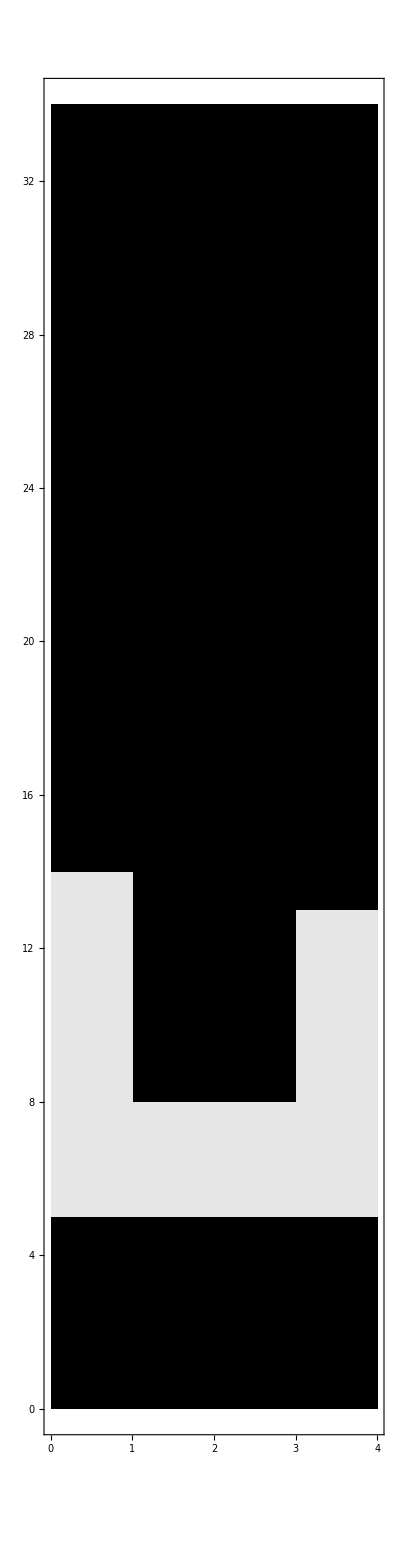
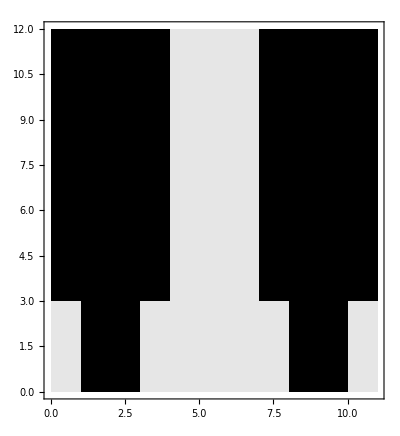
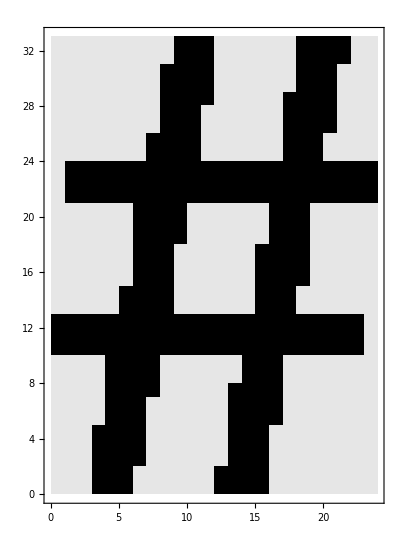
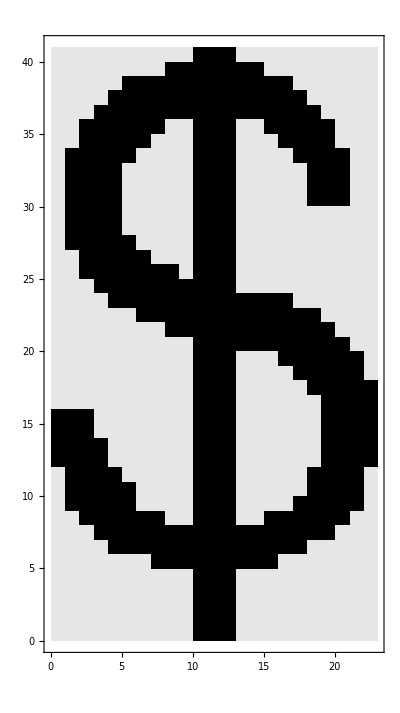
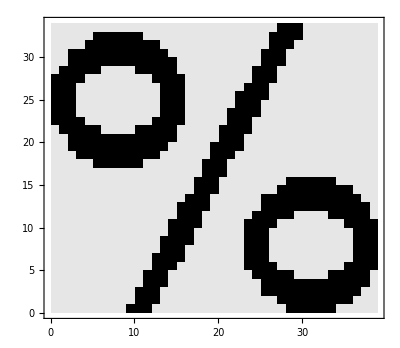
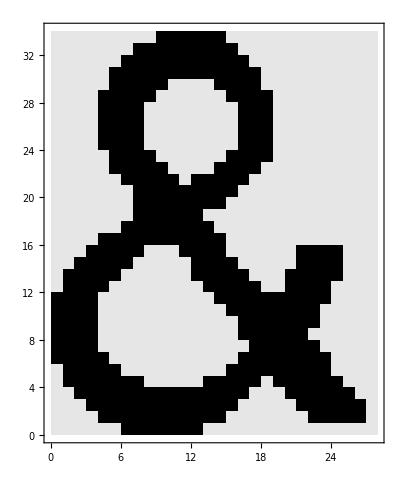
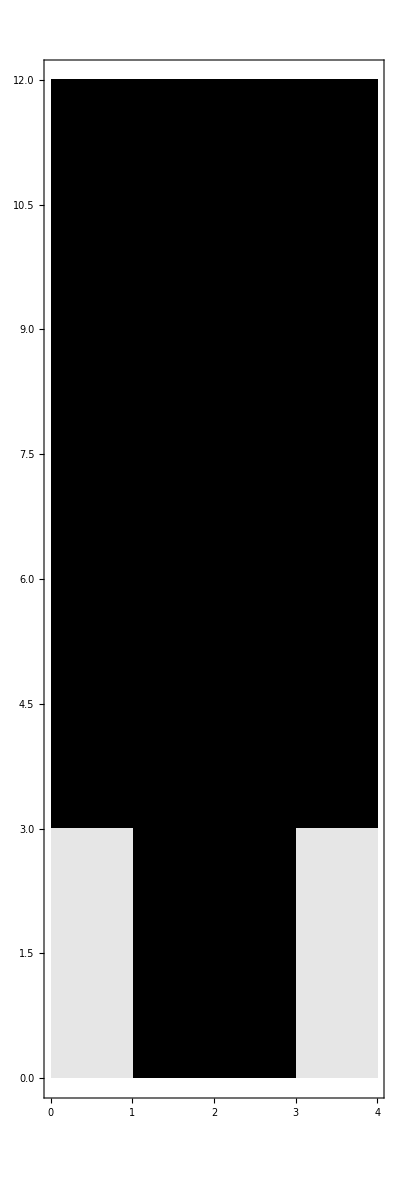
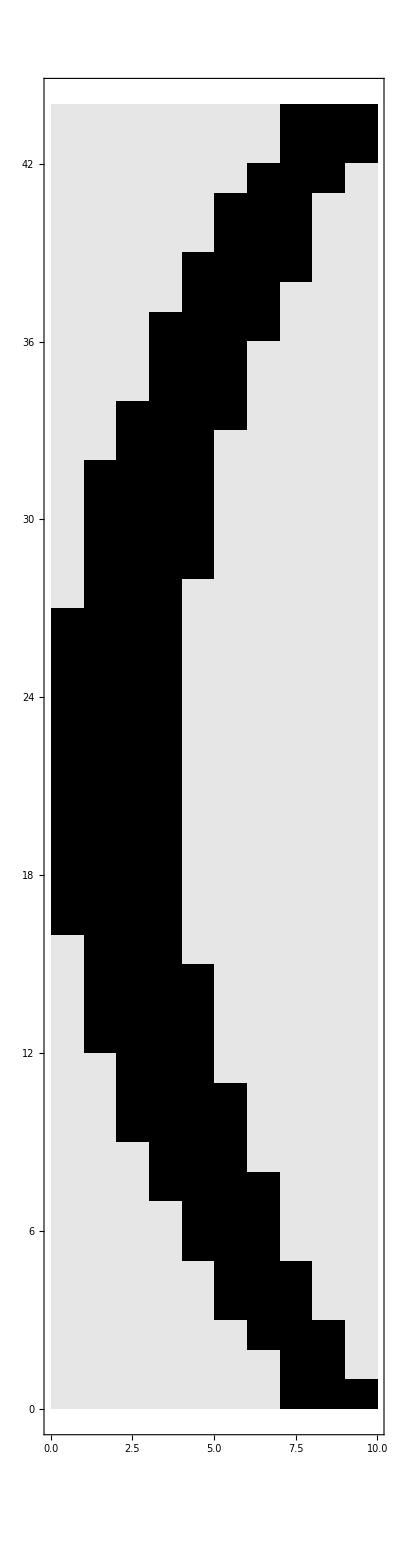
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[Raster[Reverse[.9(1-#)]],Frame->True,AspectRatio->Divide@@Dimensions[#]]&/@Rest[bitmaps]
```